## The RGB Cube corners.

```mathematica
AppendTo[$Path, ParentDirectory@NotebookDirectory[]];
<<ColorSpacePackage`
```

Piecewise::pairs: The first argument pFun_ of Piecewise is not a list of pairs.

```mathematica
Manipulate[ShowLCaCbCube3D[θ,PlotRange-> {{0,√3},{-√(2/3) Cos[π/6-Mod[-π/6+θ,π/3]],√(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]},{-√(2/3) Cos[π/6-Mod[θ,π/3]],√(2/3) Cos[π/6-Mod[θ,π/3]]}},ViewPoint->{1000,0,0}],{θ,0,Pi}]
```

```mathematica
Manipulate[ShowLCaCbCube3D[θ],{θ,0,Pi}]
```

```mathematica
ShowLCaCbCube3D[0]
```

-Graphics3D-

```mathematica
Graphics3D[LCaCbCubeFinite3D[0,8],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Graphics3D[Flatten[{EdgeForm[],Opacity[.7],LCaCbCubeFinite3D[0,8]}],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Graphics3D[RGBCubeInYabFiniteBalls[0,3,8],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Graphics3D[RGBCubeInYabFiniteBalls[0,3,8,{0.8,0.01}],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Graphics3D[Flatten[{EdgeForm[],Opacity[.7],RGBCubeFinite3D[8]}],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
LCaCbColorTheta=2
```

```mathematica
Block[{l=0.5,n=16},
Grid[Table[LCaCbColorFast[l,a,b],{a,0,1,1/n},{b,0,1,1/n}],Spacings->{0,-0.2}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{n=2^8/2^3;,θ=0},
LCaCbColorTheta=θ;
Graphics3D[{Opacity[.7],Raster3D[Table[LCaCbColorFastList[k,j,i],{i,0,1,1/n},{j,0,1,1/n},{k,0,1,1/n}],ColorFunction->Hue]},GraphicsCubeOpts]
]
```

-Graphics3D-

```mathematica
GraphicsRow[{Graphics3D[RGBCubeFinite3D[8],GraphicsCubeOptions[Axes->True,AxesLabel->{"Red","Green","Blue"}]],
Graphics3D[RGBCube3D[RGBCube["RGB"]],Axes->True,AxesLabel->{"Red","Green","Blue"},GraphicsCubeOpts]
}]
```

-Graphics-

```mathematica
Block[{n=10,θ=0,cube,m=24,steps,imgSize=500},
(* cube=RGBCubeFinite3D[n]; *)
cube=RGBCube3D[RGBCube["RGB"]];
steps=Flatten[{
Table[Graphics3D[Rotate[Rotate[Rotate[cube,g,{0,1,0}],0,{0,0,1}],0,{1,0,0}],Axes->True,PlotRange->{{0,Sqrt[3]},{-1,1},{-1,1}},ImageSize->imgSize,GraphicsCubeOpts],{g,0,Pi/4,Pi/(4m)}],
Table[Graphics3D[Rotate[Rotate[Rotate[cube,Pi/4,{0,1,0}],b,{0,0,1}],0,{1,0,0}],Axes->True,PlotRange->{{0,Sqrt[3]},{-1,1},{-1,1}},ImageSize->imgSize,GraphicsCubeOpts],{b,0,-ArcTan[1/Sqrt[2]],-ArcTan[1/Sqrt[2]]/m}],
Table[Graphics3D[Rotate[Rotate[Rotate[cube,Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],r,{1,0,0}],Axes->True,PlotRange->{{0,Sqrt[3]},{-1,1},{-1,1}},ImageSize->imgSize,GraphicsCubeOpts],{r,0,Pi/4,Pi/(4m)}]
}];
ListAnimate[steps,AnimationRepetitions->1,AnimationRunning->False,AnimationRate->m,AnimationDirection->ForwardBackward]
]
```

```mathematica
Graphics3D[{Opacity[.7],RGBCubeInYabFinite[θ,3]},GraphicsCubeOptions[ViewPoint->{Infinity,0,0}]]/.θ->0
```

-Graphics3D-

## Rotation Matrices

Any 3 D rotation can be expressed as the product of 3 rotations about the cartesian axis.

```mathematica
ShowFun[RotationMatrixX[α]]
ShowFun[RotationMatrixY[β]]
ShowFun[RotationMatrixZ[γ]]
```

R_X(α) = (1 | 0 | 0
0 | cos(α) | sin(α)
0 | -sin(α) | cos(α))

R_Y(β) = (cos(β) | 0 | -sin(β)
0 | 1 | 0
sin(β) | 0 | cos(β))

R_Z(γ) = (cos(γ) | sin(γ) | 0
-sin(γ) | cos(γ) | 0
0 | 0 | 1)

```mathematica
Row[{MatrixForm[RotationMatrixX[α]],".",MatrixForm[RotationMatrixZ[γ]],".",MatrixForm[RotationMatrixY[β]]," =",MatrixForm[RotationMatrixXYZ[α,β, γ]]}]
```

(1 | 0 | 0
0 | Cos[α] | Sin[α]
0 | -Sin[α] | Cos[α]).(Cos[γ] | Sin[γ] | 0
-Sin[γ] | Cos[γ] | 0
0 | 0 | 1).(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β]) =(1/2 (Cos[β-γ]+Cos[β+γ]) | Sin[γ] | 1/2 (-Sin[β-γ]-Sin[β+γ])
1/4 (2 Cos[α-β]-2 Cos[α+β]+Sin[α-β-γ]+Sin[α+β-γ]-Sin[α-β+γ]-Sin[α+β+γ]) | 1/2 (Cos[α-γ]+Cos[α+γ]) | 1/4 (-Cos[α-β-γ]+Cos[α+β-γ]+Cos[α-β+γ]-Cos[α+β+γ]+2 Sin[α-β]+2 Sin[α+β])
1/4 (Cos[α-β-γ]+Cos[α+β-γ]-Cos[α-β+γ]-Cos[α+β+γ]-2 Sin[α-β]+2 Sin[α+β]) | 1/2 (-Sin[α-γ]-Sin[α+γ]) | 1/4 (2 Cos[α-β]+2 Cos[α+β]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ]))

```mathematica
ShowFun[LCaCb[θ]]
```

R(θ) = (1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) sin(θ+π/6) | √(2/3) cos(θ) | -√(2/3) sin(π/6-θ)
-√(2/3) cos(θ+π/6) | -√(2/3) sin(θ) | √(2/3) cos(π/6-θ))

Solution for the Yab cube. Luminocity axis is in the X value.

```mathematica
Print[MatrixForm[LCaCb[θ]].MatrixForm[RGBCube],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[LCaCb[θ]. RGBCube]]],1]]
Print[MatrixForm[iLCaCb[θ]].MatrixForm[RGBCube["LCaCb"][θ]],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[iLCaCb[θ]. RGBCube["LCaCb"][θ]]]],1]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

(1/(√3) | -√(2/3) Sin[π/6+θ] | -√(2/3) Cos[π/6+θ]
1/(√3) | √(2/3) Cos[θ] | -√(2/3) Sin[θ]
1/(√3) | -√(2/3) Sin[π/6-θ] | √(2/3) Cos[π/6-θ]).(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)=(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

The inverse of a rotation is equal to the transpose of the rotation matrix

```mathematica
TrigFactor[FullSimplify[TrigToExp[Inverse[LCaCb[θ]]]]] == Transpose[LCaCb[θ]]
```

True

### Cube Corners

To get the corners of the RGBCube in RGB and LCaCb space we can use

```mathematica
Row[{"RGBCube"["RGB"]," = ", MatrixForm[RGBCube["RGB"]],"    ","RGBCube"["LCaCb"][θ]," = ", MatrixForm[RGBCube["LCaCb"][θ]]}]
```

RGBCube[RGB] = (0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)    RGBCube[LCaCb][θ] = (0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

To get the corners of the LCaCbCube in RGB and LCaCb space we can use

```mathematica
Row[{"LCaCbCube"["RGB"][0]," = ", MatrixForm[LCaCbCube["RGB"][0]],"    ","LCaCbCube"["LCaCb"][0]," = ", MatrixForm[LCaCbCube["LCaCb"][0]]}]
```

```mathematica
"LCaCbCube"["RGB"][0]" = "({{5/6, 11/6, 7/6, 1/6, -5/6, -1/6, 5/6, 1/6}, {-2/3, 1/3, 5/3, 2/3, 2/3, -2/3, 1/3, 5/3}, {-1/6, 5/6, 1/6, -5/6, 1/6, 5/6, 11/6, 7/6}})"    ""LCaCbCube"["LCaCb"][0]" = "({{0, √3, √3, 0, 0, 0, √3, √3}, {-√(2/3), -√(2/3), √(2/3), √(2/3), √(2/3), -√(2/3), -√(2/3), √(2/3)}, {-1/(√2), -1/(√2), -1/(√2), -1/(√2), 1/(√2), 1/(√2), 1/(√2), 1/(√2)}})
```

#### Axis Ranges

Functionally the axis ranges for the Yab axis are given by

```mathematica
TraditionalForm[Row[{scale["LCaCb","nLCaCb"]["θ"]," = ",MatrixForm@scale["LCaCb","nLCaCb"][θ],"           ",
scale["nLCaCb","LCaCb"]["θ"]," = ",MatrixForm@scale["nLCaCb","LCaCb"][θ]}]]
TraditionalForm[Row[{scale["LCaCb","nLCaCb"]["θ"]," = ",MatrixForm@scale["LCaCb","nLCaCb"][θ, θ2m1, θ2],"           ",
scale["nLCaCb","LCaCb"]["θ"]," = ",MatrixForm@scale["nLCaCb","LCaCb"][θ, θ2m1, θ2],"      where     ",
Column[{Row[{θ2m1," = ",Mod[θ - Pi/6, Pi/3]}],Row[{θ2," = ",Mod[θ, Pi/3]}]}]}]]
```

L(θ) = (√3
2 √(2/3) cos(π/6-(θ-π/6)π/3)
2 √(2/3) cos(π/6-θπ/3))           L^-1(θ) = (1/(√3)
1/2 √(3/2) sec(π/6-(θ-π/6)π/3)
1/2 √(3/2) sec(π/6-θπ/3))

L(θ) = (√3
2 √(2/3) cos(π/6-θ_2^-1)
2 √(2/3) cos(π/6-θ_2))           L^-1(θ) = (1/(√3)
1/2 √(3/2) sec(π/6-θ_2^-1)
1/2 √(3/2) sec(π/6-θ_2))      where     θ_2^-1 = (θ-π/6)π/3
θ_2 = θπ/3

```mathematica
TableForm[LCaCbAxisRanges[θ],TableHeadings->{{"L","Ca","Cb"},{"Min","Max"}},TableAlignments->Center]
```

| Min | Max
L | 0 | √3
Ca | -√(2/3) Cos[π/6-Mod[-π/6+θ,π/3]] | √(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]
Cb | -√(2/3) Cos[π/6-Mod[θ,π/3]] | √(2/3) Cos[π/6-Mod[θ,π/3]]

```mathematica
Manipulate[Block[{maxRanges,ranges, cube},
maxRanges = {{0,√3},{-√(2/3),√(2/3)},{-√(2/3),√(2/3)}};
ranges = scale["LCaCb","nLCaCb"][θ];
cube = Cuboid[{{ranges[[1,1]],ranges[[2,1]],ranges[[3,1]]},{ranges[[1,2]],ranges[[2,2]],ranges[[3,2]]}}];
Grid[{{Show[
Graphics[Raster[Table[Table[inLCaCb[θ].{Y,a,b},{a,-0.5,0.5,0.02}],{b,-0.5,0.5,0.02}]]]
,ImageSize->400],Graphics[{Black,Rectangle[Sequence@@Transpose[{LCaCbAxisRanges[θ][[2]],LCaCbAxisRanges[θ][[3]]}]],Blue,Polygon[LCaCbPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube["RGB"]][[{2,3,4,5,6,7}]]]]]},PlotRange->{maxRanges[[2]],maxRanges[[3]]},ImageSize->400]}}]
],{θ,0,Pi},{{Y,0.5},0,1}]
```

```mathematica
Clear[theta]
```

```mathematica
cube3D=Flatten[{Opacity[1],RGBCubeInYabFinite[0,Sqrt[3]],LCaCbAxisEnds3D[0,3]}]
```

Table::iterb: Iterator {k, 0, 1, 1/n} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

{Opacity[1],Raster3D[Table[{i,j,k,If[i+j+k<√3,1,0.03]},{k,0,1,1/n},{j,0,1,1/n},{i,0,1,1/n}],{{0,0,0},{1,1,1}},ColorFunction→RGBColor],Glow[-Graphics-],-Graphics-,Cylinder[{{0,0,0},{0.001,0,0}},0.1],Glow[-Graphics-],-Graphics-,Cylinder[{{√3,0,0},{1.73105,0,0}},0.1],Glow[Hue[0.833333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,-√(2/3),0},{(√3)/2,-0.815497,0}},0.1],Glow[Hue[0.333333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,√(2/3),0},{(√3)/2,0.815497,0}},0.1],Glow[Hue[0.0833333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,0,-1/(√2)},{(√3)/2,0,-0.706107}},0.1],Glow[Hue[0.583333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,0,1/(√2)},{(√3)/2,0,0.706107}},0.1]}

```mathematica
Manipulate[Block[{maxRanges, ranges, cube, centersB, centersA, cols, imgScale, ticks,CbWidth,CbHeight,Cb,CaWidth,CaHeight,Ca,opt,cube3D}, 
   MaxTheta = Pi/2+0.2;
maxRanges = {{0, Sqrt[3]}, {-Sqrt[2/3], Sqrt[2/3]}, {-Sqrt[2/3], Sqrt[2/3]}};
imgScale = 200;
ranges = scale["LCaCb","nLCaCb"][θ]; 
  cube = Cuboid[{{ranges[[1,1]], ranges[[2,1]], ranges[[3,1]]}, {ranges[[1,2]], ranges[[2,2]], ranges[[3,2]]}}]; 
  centersB = RGBCube["LCaCb"][θ][[3]];
centersA = RGBCube["LCaCb"][θ][[2]]; 
cols = MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]]; 
  ticks =Prepend[ Table[{N[i*(Pi/6)], i*(Pi/6)}, {i, 0, 6*(MaxTheta/Pi)}],{N[θ],"θ"}];
CbWidth  = maxRanges[[2,2]] - maxRanges[[2,1]] + MaxTheta; 
  CbHeight = maxRanges[[3,2]] - maxRanges[[3,1]];
Cb = Plot[Evaluate[RGBCube["LCaCb"][theta][[3]]], {theta, 0, MaxTheta}, 
         PlotStyle -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]], 
     FrameTicks -> {{All, None}, {None,ticks}}, 
         FrameLabel -> { {"RGB Cube corner position in Cb",None},{None,None}}, 
     PlotRange -> {{0, MaxTheta - maxRanges[[2,1]] + maxRanges[[2,2]]}, maxRanges[[3]]}, 
         Frame -> True, 
     Epilog -> Flatten[{Line[{{θ, -Sqrt[2/3]}, {θ, Sqrt[2/3]}}],
    {Opacity[0.8],  Table[{cols[[i]], Disk[{θ, centersB[[i]]}, 0.04]}, {i, 1, 8}]}, 
           {Black, Translate[Rectangle[Sequence @@ Transpose[{scale["LCaCb","nLCaCb"][θ][[2]], scale["LCaCb","nLCaCb"][θ][[3]]}]], {MaxTheta - maxRanges[[2,1]], 0}], 
            Blue, Translate[
          Polygon[LCaCbPolygon[θ], VertexColors -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]][[{2, 3, 4, 5, 6, 7}]]]]],
          {MaxTheta - maxRanges[[2,1]], 0}]
   }}], 
  AspectRatio -> CbHeight/CbWidth, 
      ImageSize -> Floor[imgScale*{CbWidth, CaHeight}]
]; 
CaWidth = maxRanges[[3,2]] - maxRanges[[3,1]] + MaxTheta; 
  CaHeight = maxRanges[[2,2]] - maxRanges[[2,1]];
Ca = Plot[Evaluate[RGBCube["LCaCb"][theta][[2]]], {theta, 0, MaxTheta}, 
         PlotStyle -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]], 
     FrameTicks -> {{All, None}, {ticks, None}}, 
         FrameLabel -> {None, "RGB Cube corner position in Ca"}, 
     PlotRange -> {{0, MaxTheta - maxRanges[[3,1]] + maxRanges[[3,2]]}, maxRanges[[2]]}, 
         Frame -> True, 
     Epilog -> Flatten[{Line[{{θ, -Sqrt[2/3]}, {θ, Sqrt[2/3]}}], 
    {Opacity[0.8], Table[{cols[[i]], Disk[{θ, centersA[[i]]}, 0.04]}, {i, 1, 8}]}, 
           {Black, Translate[Rectangle[Sequence @@ Transpose[{scale["LCaCb","nLCaCb"][θ][[3]], scale["LCaCb","nLCaCb"][θ][[2]]}]], {MaxTheta - maxRanges[[3,1]], 0}], 
            Blue, Translate[Polygon[LCaCbPolygon[θ - Pi/2], VertexColors -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]][[
                {2, 3, 4, 5, 6, 7}]]]]], {MaxTheta - maxRanges[[3,1]], 0}]}}], 
     AspectRatio -> CaHeight/CaWidth, 
         ImageSize -> Floor[imgScale*{CaWidth, CaHeight}]
   ]; 

opt=GraphicsCubeOptions[ PlotRange->scale["LCaCb","nLCaCb"][θ],ViewPoint->{8,5,-10},ImageSize->500];

cube3D=Flatten[{Opacity[1],RGBCubeInYabFinite[θ,cut],LCaCbAxisEnds3D[θ,brighten]}];

    Row[{Graphics3D[cube3D,opt],Show[Graphics[{
Inset[Cb, Floor[imgScale*{CbWidth, 0}], {CbWidth, maxRanges[[3,1]]}, Floor[imgScale*{CbWidth, CbHeight}]], 
       Inset[Ca, Floor[imgScale*{CaWidth, 0}], {CaWidth, maxRanges[[2,2]]}, Floor[imgScale*{CaWidth, CaHeight}], {0, -1}]}], 
     PlotRange -> Floor[imgScale*{{0, CbWidth}, {0, CaWidth}}],ImageSize->500]}]
]
, {θ, 0, MaxTheta},{brighten,1,2},{{cut,3},0,3}]
```

```mathematica
eq=Map[(0≤#≤1)&,iLCaCb[θ].{y,a,b}];
MatrixForm[eq]
```

(0≤y/(√3)-√(2/3) b Cos[π/6+θ]-√(2/3) a Sin[π/6+θ]≤1
0≤y/(√3)+√(2/3) a Cos[θ]-√(2/3) b Sin[θ]≤1
0≤y/(√3)+√(2/3) b Cos[π/6-θ]-√(2/3) a Sin[π/6-θ]≤1)

```mathematica
eqn=Simplify[eq/.{θ->0}]
```

{-6≤√6 a+3 √2 b-2 √3 y≤0,0≤(√2 a+y)/(√3)≤1,0≤-a/(√6)+b/(√2)+y/(√3)≤1}

```mathematica
Clear[InsideCubeQ]
```

```mathematica
InsideCubeQ[{y_,a_,b_}]:=Evaluate[Reduce[Simplify[eq/.{θ->0}],{y,a,b}]]
```

```mathematica
RegionPlot3D[InsideCubeQ[{y,a,b}],{y,0,Sqrt[3]},{a,-1,1},{b,-1,1}]
```

-Graphics3D-

```mathematica
Select[{{1,1,1},{0.5,0,0}},InsideCubeQ]
```

{{0.5,0,0}}

### The unit scaled transform

```mathematica
Clear[θ]
```

It is desirable to scale the transformed color space to a known scale. This is simply achieved by scaling each axis by the reciprocal of the axis length. s(θ) = 1/(L(θ))

```mathematica
scale["nLCaCb","LCaCb"] = Function[{θ},Evaluate[Simplify[1/LCaCbAxisLengths[θ]]]];
```

```mathematica
TraditionalForm[Row[{ShowFun[scale["LCaCb","nLCaCb"][θ]],"      ",ShowFun[scale["nLCaCb","LCaCb"][θ]]}]]
```

L(θ) = {√3,2 √(2/3) cos(π/6-(θ-π/6)π/3),2 √(2/3) cos(π/6-θπ/3)}      L^-1(θ) = {1/(√3),1/2 √(3/2) sec(π/6-(θ-π/6)π/3),1/2 √(3/2) sec(π/6-θπ/3)}

```mathematica
TraditionalForm[Row[{scale["LCaCb","nLCaCb"]["θ"]," = ",MatrixForm[scale["LCaCb","nLCaCb"][θ]]}]]
TraditionalForm[Row[{scale["nLCaCb","LCaCb"]["θ"]," = ",MatrixForm[scale["nLCaCb","LCaCb"][θ]]}]]
```

L(θ) = (√3
2 √(2/3) cos(π/6-(θ-π/6)π/3)
2 √(2/3) cos(π/6-θπ/3))

L^-1(θ) = (1/(√3)
1/2 √(3/2) sec(π/6-(θ-π/6)π/3)
1/2 √(3/2) sec(π/6-θπ/3))

This produces two new transforms which are no longer rotation matrices.

  nLCaCb( θ ) = L^-1( θ ) ⊗ LCaCb( θ ) 
  
  nLCaCb^-1 = ( (L( θ ) ⊗ LCaCb( θ )   ))^T

```mathematica
Clear[inLCaCbFun,inLCaCb];
inLCaCbFun=Function[{θ},Evaluate[Transpose[scale["LCaCb","nLCaCb"][θ] LCaCb[θ]]]];
inLCaCb[θ:Except[_String]]:=inLCaCbFun[θ]
Format[inLCaCb, TraditionalForm]=Superscript[Style["nLCaCb",Bold],"-1"];
ShowFun[inLCaCb[θ]]
```

nLCaCb^-1(θ) = (1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(θ+π/6) | -4/3 cos(θ+π/6) cos(π/6-θπ/3)
1 | 4/3 cos(θ) cos(π/6-(θ-π/6)π/3) | -4/3 cos(π/6-θπ/3) sin(θ)
1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(π/6-θ) | 4/3 cos(π/6-θ) cos(π/6-θπ/3))

```mathematica
Row[{inLCaCb["θ"],".",nLCaCb["θ"]," = ",MatrixForm[FullSimplify[inLCaCb[θ] . nLCaCb[θ]]]}]
```

inLCaCb[θ].nLCaCb[θ] = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Style[TraditionalForm[Row[{nLCaCb["θ"]," = ",scale["nLCaCb","LCaCb"]["θ"]," ⊗ ",LCaCb["θ"]}]],Larger]
Style[TraditionalForm[Row[{nLCaCb["θ"]," = ",MatrixForm[scale["nLCaCb","LCaCb"][θ]]," ⊗ ",MatrixForm[LCaCb[θ]]}]],Larger]
```

nR(θ) = L^-1(θ) ⊗ R(θ)

nR(θ) = (1/(√3)
1/2 √(3/2) sec(π/6-(θ-π/6)π/3)
1/2 √(3/2) sec(π/6-θπ/3)) ⊗ (1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) sin(θ+π/6) | √(2/3) cos(θ) | -√(2/3) sin(π/6-θ)
-√(2/3) cos(θ+π/6) | -√(2/3) sin(θ) | √(2/3) cos(π/6-θ))

```mathematica
ShowFun[nLCaCb[θ]]
ShowFun[inLCaCb[θ]]
```

nR(θ) = (1/3 | 1/3 | 1/3
-1/2 sec(π/6-(θ-π/6)π/3) sin(θ+π/6) | 1/2 cos(θ) sec(π/6-(θ-π/6)π/3) | -1/2 sec(π/6-(θ-π/6)π/3) sin(π/6-θ)
-1/2 cos(θ+π/6) sec(π/6-θπ/3) | -1/2 sec(π/6-θπ/3) sin(θ) | 1/2 cos(π/6-θ) sec(π/6-θπ/3))

nLCaCb^-1(θ) = (1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(θ+π/6) | -4/3 cos(θ+π/6) cos(π/6-θπ/3)
1 | 4/3 cos(θ) cos(π/6-(θ-π/6)π/3) | -4/3 cos(π/6-θπ/3) sin(θ)
1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(π/6-θ) | 4/3 cos(π/6-θ) cos(π/6-θπ/3))

```mathematica
LxyAxisRanges
```

{√3,1.5444,1.60277}

```mathematica
Manipulate[LxyAxisRanges = Simplify[LCaCbAxisRanges[θ]];Grid[{{Graphics[{Black,Rectangle[Sequence@@Transpose[{LxyAxisRanges[[2]],LxyAxisRanges[[3]]}]],Blue,Polygon[nLCaCbPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube["RGB"]][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-1/2,1/2},{-1/2 ,1/2}}],MatrixForm[{Row[{" θ = ",θ}],Row[{LxyAxisRanges[[1,1]],"< L < ",LxyAxisRanges[[1,2]]}], Row[{LxyAxisRanges[[2,1]],"< x < ",LxyAxisRanges[[2,2]]}],Row[{LxyAxisRanges[[3,1]],"< y < ",LxyAxisRanges[[3,2]]}]}]}}],{θ,0,Pi}]
```

## Representation of the rotation

A reduced form for the matrix part of the rotation is
LCaCb( θ ) = (1/(√3)
√(2/3)
√(2/3)) ⊗ rR( θ )

```mathematica
Row[{MatrixForm[LCaCb["θ"]]," = ",MatrixForm[scale["LCaCb","rR"]["θ"]]," ⊗ ",MatrixForm[rR["θ"]]}]
Row[{MatrixForm[LCaCb[θ]]," = ",MatrixForm[scale["LCaCb","rR"][θ]],"⊗",MatrixForm[rR[θ]]}]
```

LCaCb[θ] = rS ⊗ rR[θ]

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]) = (1/(√3)
√(2/3)
√(2/3))⊗(1 | 1 | 1
-Sin[π/6+θ] | Cos[θ] | -Sin[π/6-θ]
-Cos[π/6+θ] | -Sin[θ] | Cos[π/6-θ])

```mathematica
StringJoin[mForm[scale["LCaCb","rR"]] ,"⊗", mForm[ rR[θ]],mForm[{r,g,b}]," = ",mForm[{x,y,z}]]
StringJoin[ mForm[ irR[θ]],mForm[{{mForm[scale["LCaCb","rR"]] ,"⊗",mForm[{x,y,z}]}}]," = ",mForm[{r,g,b}]]
```

( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] )⊗1 | 1 | 1
-sin(θ + π/6) | cos(θ) | -sin(π/6 - θ)
-cos(θ + π/6) | -sin(θ) | cos(π/6 - θ)r
g
b = x
y
z

1 | -sin(θ + π/6) | -cos(θ + π/6)
1 | cos(θ) | -sin(θ)
1 | -sin(π/6 - θ) | cos(π/6 - θ)( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] ) | ⊗ | x
y
z = r
g
b

Because rR is factored from a rotation matrix the inverse is

```mathematica
LCaCb^(-1 =)(({{1/(√3)}, {√(2/3)}, {√(2/3)}}) ⊗ ({{1, 1, 1}, {-Sin[π/6+θ], Cos[θ], -Sin[π/6-θ]}, {-Cos[π/6+θ], -Sin[θ], Cos[π/6-θ]}}))^T
rR =({{√3}, {√(3/2)}, {√(3/2)}}) ⊗({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}})
```

using
A = s ⊗ B    where B^-1= B^T
A^-1=  (s^-1 ⊗ B)^T

```mathematica
rR^-1 =(({{1/(√3)}, {√(2/3)}, {√(2/3)}}) ⊗({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}}))^T = ({{1/3, -2/3 Sin[π/6+θ], -2/3 Cos[π/6+θ]}, {1/3, (2 Cos[θ])/3, -(2 Sin[θ])/3}, {1/3, -2/3 Sin[π/6-θ], 2/3 Cos[π/6-θ]}})
```

Proof of inverse

```mathematica
MatrixForm[Simplify[irR[θ].rR[θ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

## Discrete Representation of the rotation

## Gaining an extra integer

rR[θ]=(1 | 1 | 1
sin(θ-(5π)/6) | sin(θ+(3π)/6) | sin(θ-π/6)
sin(θ-(2 π)/6) | sin(θ-(6 π)/6) | sin(θ+(2π)/6))

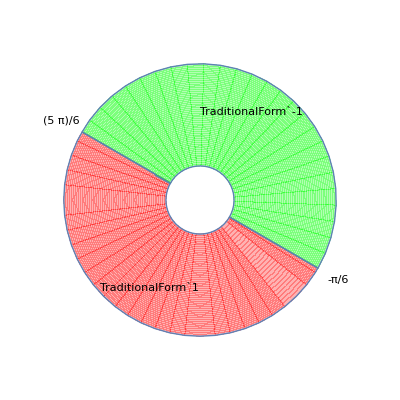
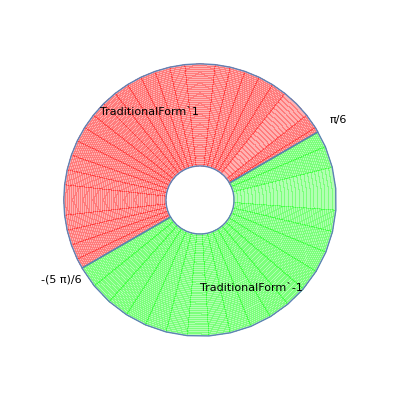
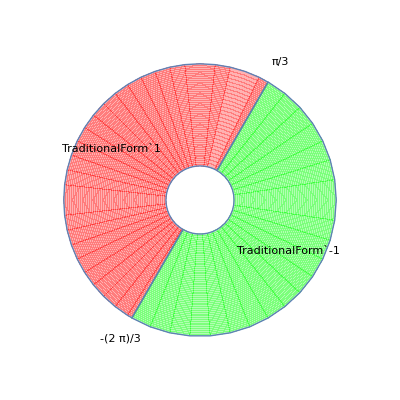
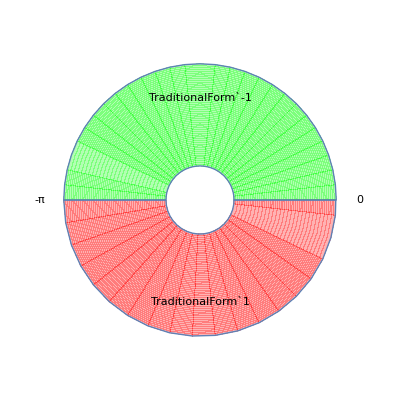
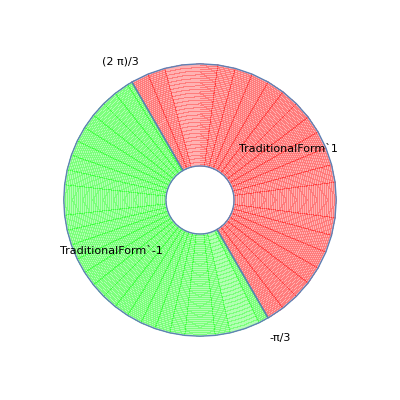
```mathematica
({{1, 1, 1}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}})
```

We have a source which makes discrete steps of 1/srcRange the question is to what degree of precision do we need to represent the transformation given that we require a precision of 1/wrkRange. What is required is the smallest number which can result from the transformation of a unit cube!

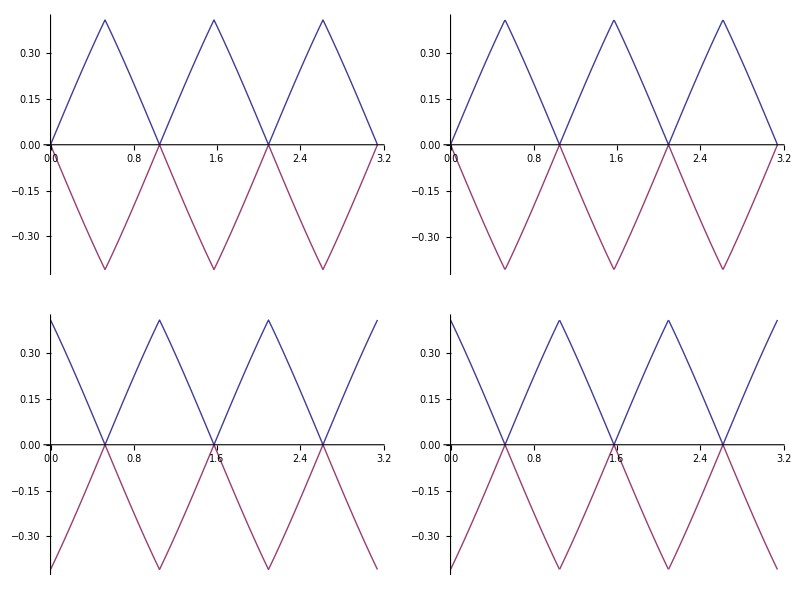

```mathematica
Grid[{{Plot[{Min[Abs[RGBCube[LCaCb][θ ][[3,{2,3,4,5,6,7}]]]],-Min[Abs[RGBCube[LCaCb][θ ][[3,{2,3,4,5,6,7}]]]]},{θ,0,Pi}], Plot[{√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]]},{θ,0,Pi}]},{Plot[{Min[Abs[RGBCube[LCaCb][θ ][[2,{2,3,4,5,6,7}]]]],-Min[Abs[RGBCube[LCaCb][θ ][[2,{2,3,4,5,6,7}]]]]},{θ,0,Pi}],Plot[{√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]]},{θ,0,Pi}]}}]
```

The error in the representation of the rotation matrix is

```mathematica
Clear[d];d[val_,n_]:=Round[(val * n)]/n;
```

```mathematica
Manipulate[StringJoin[  ToString[srcRange]," ( ",mForm[ N[d[LCaCb[θ],srcRange]]]," - ",mForm[N[LCaCb[θ]]],") = ",mForm[srcRange(N[d[LCaCb[θ],srcRange]]- N[LCaCb[θ]])]],{θ,0,Pi},{{srcRange,64},1,255,1}]
```

StringJoin::string: String expected at position 2 in "64 ( " <> mForm[0.015625\ Round[64.\ YAB[2.11743]]] <> " - " <> mForm[YAB[2.11743]] <> ") = " <> mForm[64\ (0.015625\ Round[64.\ YAB[« 1 »]] - YAB[2.11743])].

StringJoin::string: String expected at position 4 in "64 ( " <> mForm[0.015625\ Round[64.\ YAB[2.11743]]] <> " - " <> mForm[YAB[2.11743]] <> ") = " <> mForm[64\ (0.015625\ Round[64.\ YAB[« 1 »]] - YAB[2.11743])].

StringJoin::string: String expected at position 6 in "64 ( " <> mForm[0.015625\ Round[64.\ YAB[2.11743]]] <> " - " <> mForm[YAB[2.11743]] <> ") = " <> mForm[64\ (0.015625\ Round[64.\ YAB[« 1 »]] - YAB[2.11743])].

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Channels 2 and 3 sum to zero meaning that the elements always contain opposite signs.

```mathematica
maskPos=Function[{θ},Evaluate[Map[Reduce[{#1>0,0 ≤θ <2Pi},θ]&,LCaCb[θ],{2}]]];
maskNeg=Function[{θ},Evaluate[Map[Reduce[{#1<0,0 ≤θ <2Pi},θ]&,LCaCb[θ],{2}]]];
MatrixForm[maskPos[θ]]
MatrixForm[maskNeg[θ]]
```

LCaCb[θ]

LCaCb[θ]

```mathematica
LCaCb[θ]
```

```mathematica
LCaCb[θ]
```

```mathematica
partShow[Piecewise[{{mForm[Sign[nonNegativeSign[rR[Pi/12]]]], Inequality[0, LessEqual, θ, Less, Pi/6]}, 
   {mForm[Sign[nonNegativeSign[rR[Pi/4]]]], Inequality[Pi/6, LessEqual, θ, Less, Pi/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(5*Pi)/12]]]], Inequality[Pi/3, LessEqual, θ, Less, Pi/2]}, 
   {mForm[Sign[nonNegativeSign[rR[(7*Pi)/12]]]], Inequality[Pi/2, LessEqual, θ, Less, (2*Pi)/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(3*Pi)/4]]]], Inequality[(2*Pi)/3, LessEqual, θ, Less, (5*Pi)/6]}, 
   {mForm[Sign[nonNegativeSign[rR[(11*Pi)/12]]]], Inequality[(5*Pi)/6, LessEqual, θ, Less, Pi]}, 
   {mForm[Sign[nonNegativeSign[rR[(13*Pi)/12]]]], Inequality[Pi, LessEqual, θ, Less, (7*Pi)/6]}, 
   {mForm[Sign[nonNegativeSign[rR[(5*Pi)/4]]]], Inequality[(7*Pi)/6, LessEqual, θ, Less, (4*Pi)/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(17*Pi)/12]]]], Inequality[(4*Pi)/3, LessEqual, θ, Less, (3*Pi)/2]}, 
   {mForm[Sign[nonNegativeSign[rR[(19*Pi)/12]]]], Inequality[(3*Pi)/2, LessEqual, θ, Less, (5*Pi)/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(7*Pi)/4]]]], Inequality[(5*Pi)/3, LessEqual, θ, Less, (11*Pi)/6]}, 
   {mForm[Sign[nonNegativeSign[rR[(23*Pi)/12]]]], Inequality[(11*Pi)/6, LessEqual, θ, Less, 2*Pi]}}, Null]]
```

-Graphics-

```mathematica
Clear[splitCircle]
splitCircle[i_, θ_, val_:1] := Module[{showA, evalA, showB, evalB}, 
   Piecewise[{{val, CircularInequality[i*(Pi/6), LessEqual, θ, Less, (i + 6)*(Pi/6)]}, 
     {-val, CircularInequality[(i - 6)*(Pi/6), LessEqual, θ, Less, i*(Pi/6)]}}, Null]]
```

```mathematica
posNegCond=Function[{θ},Evaluate[{{1,1,1},{splitCircle[5,θ],splitCircle[9,θ],splitCircle[1,θ]},
{splitCircle[2,θ],splitCircle[6,θ,1],splitCircle[10,θ,1]}}]];
TraditionalForm[MatrixForm[posNegCond[θ]]]
```

(1 | 1 | 1
Piecewise[{{1, (5 π)/6≤θ<(11 π)/6}, {-1, -π/6≤θ<(5 π)/6}, {Null, True}}] | Piecewise[{{1, -π/2≤θ<π/2}, {-1, π/2≤θ<(3 π)/2}, {Null, True}}] | Piecewise[{{1, π/6≤θ<(7 π)/6}, {-1, -(5 π)/6≤θ<π/6}, {Null, True}}]
Piecewise[{{1, π/3≤θ<(4 π)/3}, {-1, -(2 π)/3≤θ<π/3}, {Null, True}}] | Piecewise[{{1, -π≤θ<0}, {-1, 0≤θ<π}, {Null, True}}] | Piecewise[{{1, -π/3≤θ<(2 π)/3}, {-1, (2 π)/3≤θ<(5 π)/3}, {Null, True}}])

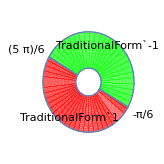
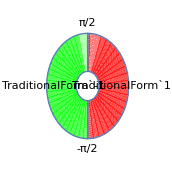
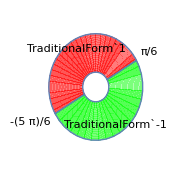
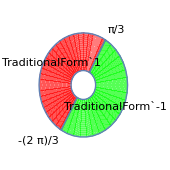
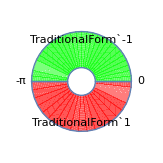
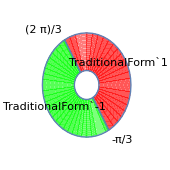
(1 | 1 | 1
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-)

```mathematica
MatrixForm[{{1,1,1},{partShow[splitCircle[5,θ]],partShow[splitCircle[9,θ]],partShow[splitCircle[1,θ]]},
{partShow[splitCircle[2,θ]],partShow[splitCircle[6,θ,1]],partShow[splitCircle[10,θ,1]]}}]
```

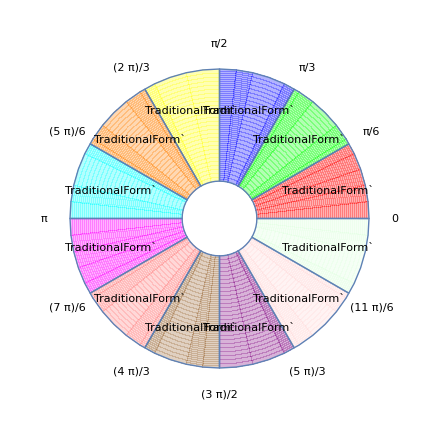

```mathematica
partShow[Piecewise[Table[{mForm[posNegCond[i Pi/6+Pi/12]], Inequality[i Pi/6, LessEqual, θ, Less, (i+1) Pi/6]},{i,0,11}], Null]]
```

To trace the origin of the error we need to know which elements in a row share the same sign.

```mathematica
Manipulate[{StringJoin["R[",ToString[θ,TraditionalForm],"] = ",mForm[colorMat[rR[θ]]]],StringJoin[ToString[1/2,TraditionalForm],"(",mForm[Sign[nonNegativeSign[rR[θ]].{1,1,1}]],"⊗",mForm[nonNegativeSign[rR[θ]]],"+1) = "," = ",mForm[matSameSign[rR[θ]]]]},{θ,0,2 Pi,Pi/12}]
```

StringJoin::string: String expected at position 2 in "R[\!\(TraditionalForm\`\(2\\ \[Pi]\)\/3\)] = " <> mForm[colorMat[rR[2\ π/3]]].

StringJoin::string: String expected at position 2 in "\!\(TraditionalForm\`1\/2\)(" <> mForm[Sign[nonNegativeSign[rR[2\ π/3]] . {1, 1, 1}]] <> "\[CircleTimes]" <> mForm[nonNegativeSign[rR[2\ π/3]]] <> "+1) =  = " <> mForm[matSameSign[rR[2\ π/3]]].

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

```mathematica
partShow[Piecewise[{
{mForm[matSameSign[rR[Pi/12]]], Inequality[0, LessEqual, θ, Less, Pi/6]||Inequality[         Pi       , LessEqual, θ, Less, (7*Pi)/6]}, 
   {mForm[matSameSign[rR[        Pi   /  4  ]]], Inequality[        Pi/  6, LessEqual, θ, Less, Pi/3]||Inequality[(7*Pi)/6, LessEqual, θ, Less, (4*Pi)/3]}, 
   {mForm[matSameSign[rR[(  5*Pi)/12]]], Inequality[        Pi/  3, LessEqual, θ, Less, Pi/2]||Inequality[(4*Pi)/3, LessEqual, θ, Less, (3*Pi)/2]}, 
   {mForm[matSameSign[rR[(  7*Pi)/12]]], Inequality[        Pi/  2, LessEqual, θ, Less, (2*Pi)/3]||Inequality[(3*Pi)/2, LessEqual, θ, Less, (5*Pi)/3]}, 
   {mForm[matSameSign[rR[(  3*Pi)/  4]]], Inequality[(2*Pi)/3, LessEqual, θ, Less, (5*Pi)/6]||Inequality[(5*Pi)/3, LessEqual, θ, Less, (11*Pi)/6]}, 
   {mForm[matSameSign[rR[(11*Pi)/12]]], Inequality[(5*Pi)/6, LessEqual, θ, Less, Pi]||Inequality[(11*Pi)/6, LessEqual, θ, Less, 2*Pi]}}, Null]]
```

-Graphics-

```mathematica
sameLoc[θ_]:=Piecewise[{{{Null,2,3}, Inequality[0, LessEqual, θ, Less, Pi/6] || Inequality[Pi, LessEqual, θ, Less, (7*Pi)/6]}, 
   {{Null,1,3}, Inequality[Pi/6, LessEqual, θ, Less, Pi/3] || Inequality[(7*Pi)/6, LessEqual, θ, Less, (4*Pi)/3]}, 
   {{Null,1,2}, Inequality[Pi/3, LessEqual, θ, Less, Pi/2] || Inequality[(4*Pi)/3, LessEqual, θ, Less, (3*Pi)/2]}, 
   {{Null,3,2}, Inequality[Pi/2, LessEqual, θ, Less, (2*Pi)/3] || Inequality[(3*Pi)/2, LessEqual, θ, Less, (5*Pi)/3]}, 
   {{Null,3,1}, Inequality[(2*Pi)/3, LessEqual, θ, Less, (5*Pi)/6] || Inequality[(5*Pi)/3, LessEqual, θ, Less, (11*Pi)/6]}, 
   {{Null,2,1}, Inequality[(5*Pi)/6, LessEqual, θ, Less, Pi] || Inequality[(11*Pi)/6, LessEqual, θ, Less, 2*Pi]}}, Null]
```

Clear::ssym: scale["rR", "fR"] is not a symbol or a string.

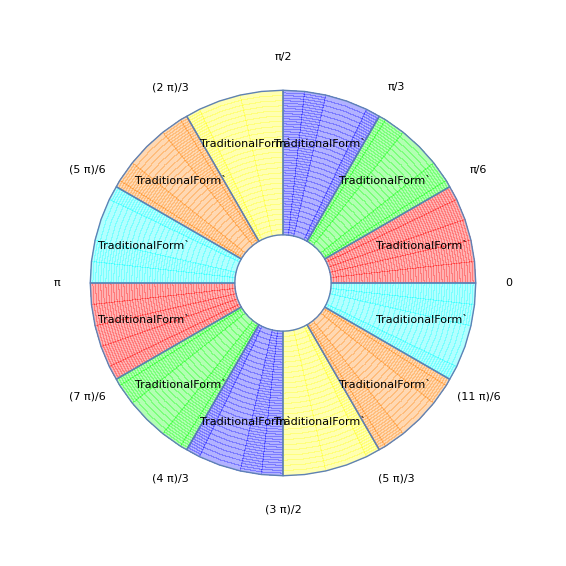

```mathematica
Clear[scale["rR","fR"],θ];
scale["rR","fR"]=Function[θ,Evaluate[Piecewise@Table[{{1,rR[θ]⟦2,sameLoc[i]⟦2⟧⟧,rR[θ]⟦3,sameLoc[i]⟦3⟧⟧},i-π/12≤Mod[θ,2 Pi]<i+π/12||i+(11 π)/12≤Mod[θ,2 Pi]<i+(13 π)/12},{i,π/12,(11 π)/12,π/6}]]];
partShow[ApplyToPiecewise[mForm,scale["rR","fR"][θ]]]
```

```mathematica
fR=Function[{θ},Evaluate[ApplyToPiecewise[(rR[θ]/#)&,scale["rR","fR"][θ]]]];
```

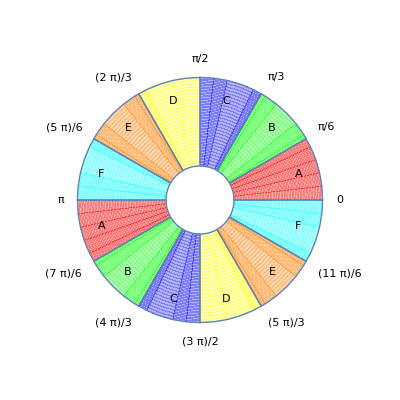
The Factored Rotation in each π/6 Region
-Graphics- | Scale : fS[θ] | Factored Rotation : fR[θ]
A | 1
cos(θ)
cos(π/6 - θ) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
B | 1
-sin(θ + π/6)
cos(π/6 - θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
C | 1
-sin(θ + π/6)
-sin(θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
D | 1
-sin(π/6 - θ)
-sin(θ) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
E | 1
-sin(π/6 - θ)
-cos(θ + π/6) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))
F | 1
cos(θ)
-cos(θ + π/6) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[scale["rR","fR"][θ][[1,1,1]]],TraditionalForm[fR[θ][[1,1,1]]]},
{mForm[scale["rR","fR"][θ][[1,2,1]]],TraditionalForm[fR[θ][[1,2,1]]]},
{mForm[scale["rR","fR"][θ][[1,3,1]]],TraditionalForm[fR[θ][[1,3,1]]]},
{mForm[scale["rR","fR"][θ][[1,4,1]]],TraditionalForm[fR[θ][[1,4,1]]]},
{mForm[scale["rR","fR"][θ][[1,5,1]]],TraditionalForm[fR[θ][[1,5,1]]]},
{mForm[scale["rR","fR"][θ][[1,6,1]]],TraditionalForm[fR[θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fS[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

Let θ1 = Mod[θ,Pi/6]
Let Θ = θ-θ1
then
θ = Θ+θ1
also the regions can be simplified by noticing that they are in modulo π arithmatic so θ→Mod[θ,π]

```mathematica
ffR=Function[{θ},Evaluate[
Piecewise@Table[{Assuming[Element[θ1,Reals]&& θ1≥ 0 && θ1< Pi/6,FullSimplify[fR[θ][[1,i+1,1]]/.{θ->i Pi/6 +θ1}]],FullSimplify[fR[θ][[1,i+1,2,1]]/.{Mod[θ,2 π]-> Mod[θ,π]} ]},{i,0,5}]]];
```

```mathematica
Definition[ffR]
```

```mathematica
ApplyToPiecewise[mForm,ffR[θ]]
```

Piecewise[{{1 | 1 | 1
sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1)
-cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1))
1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1))
sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
-cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1
sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1), π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1
1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1)
1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

There are only 4 functions

```mathematica
Clear[ffRList,fReq,fRe,ffRe]
```

```mathematica
ffRList=Function[{δθ},Evaluate@ApplyToPiecewise[Union[Flatten[#]]&,ffR[θ]][[1,1,1]]]
```

Function[{δθ},{1,-Cos[π/6+δθ] Sec[π/6-δθ],-Sec[π/6-δθ] Sin[δθ],-Sec[δθ] Sin[π/6+δθ],1/2 (-1+√3 Tan[δθ])}]

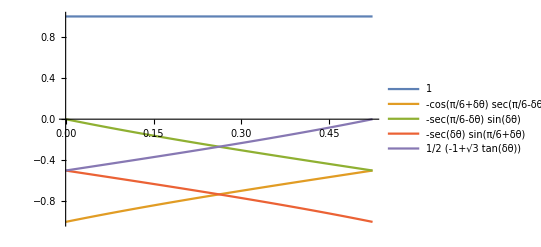

```mathematica
Plot[Evaluate[ffRList[δθ]],{δθ,0,Pi/6},PlotLegends->"Expressions"]
```

using

```mathematica
If[FullSimplify[#],TraditionalForm[#]]&[-Cos[π/6+θ1] Sec[π/6-θ1]==-1/2 (1+√3 Tan[π/6-θ1])]
If[FullSimplify[#],TraditionalForm[#]]&[-Sec[π/6-θ1] Sin[θ1] ==-1/2 (1+√3 Tan[θ1-π/6])]
If[FullSimplify[#],TraditionalForm[#]]&[-Sec[θ1] Sin[π/6+θ1]==-1/2 (1+√3 Tan[θ1])]
```

-cos(θ_1+π/6) sec(π/6-θ_1)==1/2 (-√3 tan(π/6-θ_1)-1)

sin(θ_1) (-sec(π/6-θ_1))==1/2 (√3 tan(π/6-θ_1)-1)

sin(θ_1+π/6) (-sec(θ_1))==1/2 (-√3 tan(θ_1)-1)

Defining a common function for the elements

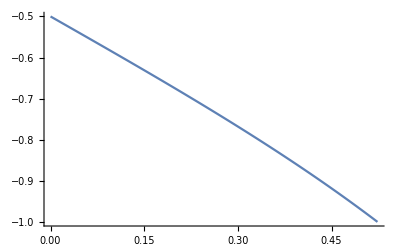

```mathematica
fRe=Function[{θ},-1/2 (1+√3 Tan[θ])];
Plot[Evaluate[fRe[θ]],{θ,0,Pi/6},PlotLegends->"Expressions"]
```

```mathematica
fReList=Function[{θ1},{fRe[π/6-θ1],fRe[θ1-π/6],fRe[θ1],fRe[-θ1]}];
Plot[Evaluate[fReList[θ1]],{θ1,0,Pi/6},PlotLegends->"Expressions"]
```

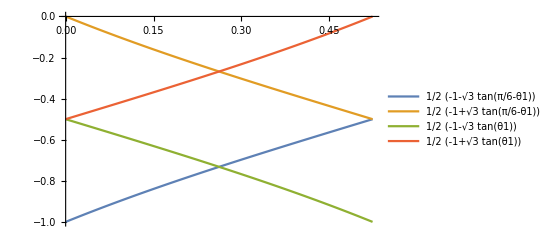

we can write fR as

```mathematica
ffRe=Function[{θ,θ1,fReqq},Evaluate[ApplyToPiecewise[
(#/.{-Cos[π/6+θ1] Sec[π/6-θ1]-> fReqq[π/6-θ1],-Sec[π/6-θ1] Sin[θ1]-> fReqq[θ1-π/6],-Sec[θ1] Sin[π/6+θ1]-> fReqq[θ1],1/2 (-1+√3 Tan[θ1])-> fReqq[-θ1]})&,ffR[θ]]]];
```

```mathematica
ffRe=Function[{θ,θ1,fReqq},Piecewise[{{{{1,1,1},{fReqq[θ1],1,fReqq[-θ1]},{fReqq[π/6-θ1],fReqq[-π/6+θ1],1}},0≤Mod[θ,π]<π/6},{{{1,1,1},{1,fReqq[π/6-θ1],fReqq[-π/6+θ1]},{fReqq[-θ1],fReqq[θ1],1}},π/6≤Mod[θ,π]<π/3},{{{1,1,1},{1,fReqq[-θ1],fReqq[θ1]},{fReqq[-π/6+θ1],1,fReqq[π/6-θ1]}},π/3≤Mod[θ,π]<π/2},{{{1,1,1},{fReqq[π/6-θ1],fReqq[-π/6+θ1],1},{fReqq[θ1],1,fReqq[-θ1]}},π/2≤Mod[θ,π]<(2 π)/3},{{{1,1,1},{fReqq[-θ1],fReqq[θ1],1},{1,fReqq[π/6-θ1],fReqq[-π/6+θ1]}},(2 π)/3≤Mod[θ,π]<(5 π)/6},{{{1,1,1},{fReqq[-π/6+θ1],1,fReqq[π/6-θ1]},{1,fReqq[-θ1],fReqq[θ1]}},(5 π)/6≤Mod[θ,π]<π}},0]];
```

```mathematica
ApplyToPiecewise[mForm,ffRe[θ,θ1,fRe]]
```

Piecewise[{{1 | 1 | 1
1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1)
1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) - 1)
1/2 (√3 tan(TraditionalForm`θ_1) - 1) | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1) | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1)
1/2 (√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1), π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1
1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1), π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
1/2 (√3 tan(TraditionalForm`θ_1) - 1) | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1
1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) - 1), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
1/2 (√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1)
1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1) | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
Row[{"fR(θ) = ",ApplyToPiecewise[mForm,ffRe[θ,θ1,"fRe"]]}]
```

fR(θ) = Piecewise[{{1 | 1 | 1
fRe | 1 | fRe
fRe | fRe | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | fRe | fRe
fRe | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | fRe | fRe
fRe | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
fRe | fRe | 1
fRe | 1 | fRe, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
fRe | fRe | 1
1 | fRe | fRe, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
fRe | 1 | fRe
1 | fRe | fRe, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[scale["rR","fR"][θ][[1,1,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,1,1]]]},
{mForm[scale["rR","fR"][θ][[1,2,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,2,1]]]},
{mForm[scale["rR","fR"][θ][[1,3,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,3,1]]]},
{mForm[scale["rR","fR"][θ][[1,4,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,4,1]]]},
{mForm[scale["rR","fR"][θ][[1,5,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,5,1]]]},
{mForm[scale["rR","fR"][θ][[1,6,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fS[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The Factored Rotation in each π/6 Region
-Graphics- | Scale : fS[θ] | Factored Rotation : fR[θ]
A | 1
cos(θ)
cos(π/6 - θ) | (1 | 1 | 1
fRe(θ_1) | 1 | fRe(-θ_1)
fRe(π/6-θ_1) | fRe(θ_1-π/6) | 1)
B | 1
-sin(θ + π/6)
cos(π/6 - θ) | (1 | 1 | 1
1 | fRe(π/6-θ_1) | fRe(θ_1-π/6)
fRe(-θ_1) | fRe(θ_1) | 1)
C | 1
-sin(θ + π/6)
-sin(θ) | (1 | 1 | 1
1 | fRe(-θ_1) | fRe(θ_1)
fRe(θ_1-π/6) | 1 | fRe(π/6-θ_1))
D | 1
-sin(π/6 - θ)
-sin(θ) | (1 | 1 | 1
fRe(π/6-θ_1) | fRe(θ_1-π/6) | 1
fRe(θ_1) | 1 | fRe(-θ_1))
E | 1
-sin(π/6 - θ)
-cos(θ + π/6) | (1 | 1 | 1
fRe(-θ_1) | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | fRe(θ_1-π/6))
F | 1
cos(θ)
-cos(θ + π/6) | (1 | 1 | 1
fRe(θ_1-π/6) | 1 | fRe(π/6-θ_1)
1 | fRe(-θ_1) | fRe(θ_1))

The Relationship

```mathematica
Reduce[-1-fRe[θ]==fRe[-θ]]
```

True

alows us to write another interesting form

```mathematica
ffRe=Function[{θ,θ1,fReqq},Evaluate[ApplyToPiecewise[
(#/.{ fReqq[θ1-π/6]-> -1-fReqq[π/6-θ1], fReqq[-θ1]-> -1-fReqq[θ1]})&,ffRe[θ,θ1,fReqq]]]];
```

```mathematica
Row[{"fR(θ) = ",ApplyToPiecewise[mForm,ffRe[θ,θ1,"fRe"]]}]
```

fR(θ) = Piecewise[{{1 | 1 | 1
fRe | 1 | -
fRe | - | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | fRe | -
- | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
- | fRe | 1
1 | fRe | -, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
- | 1 | fRe
1 | - | fRe, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
fRe=Function[{θ},-1/2 (1+√3 Tan[θ])];
fREqnForm=Function[{θ6,θ1,fReqq},Piecewise[{{{{1,1,1},{fReqq[θ1],1,-1-fReqq[θ1]},{fReqq[π/6-θ1],-1-fReqq[π/6-θ1],1}},0≤θ6<π/6},{{{1,1,1},{1,fReqq[π/6-θ1],-1-fReqq[π/6-θ1]},{-1-fReqq[θ1],fReqq[θ1],1}},π/6≤θ6<π/3},{{{1,1,1},{1,-1-fReqq[θ1],fReqq[θ1]},{-1-fReqq[π/6-θ1],1,fReqq[π/6-θ1]}},π/3≤θ6<π/2},{{{1,1,1},{fReqq[π/6-θ1],-1-fReqq[π/6-θ1],1},{fReqq[θ1],1,-1-fReqq[θ1]}},π/2≤θ6<(2 π)/3},{{{1,1,1},{-1-fReqq[θ1],fReqq[θ1],1},{1,fReqq[π/6-θ1],-1-fReqq[π/6-θ1]}},(2 π)/3≤θ6<(5 π)/6},{{{1,1,1},{-1-fReqq[π/6-θ1],1,fReqq[π/6-θ1]},{1,-1-fReqq[θ1],fReqq[θ1]}},(5 π)/6≤θ6<π}},0]];
Clear[fR]
fR[θ6_,θ1_,fReqq_]:=fREqnForm[θ6,θ1,fReqq];
fR[θ_,fReqq_]:=fREqnForm[Mod[θ,π],Mod[θ,π/6],fReqq];
fR[θ_]:=fREqnForm[Mod[θ,π],Mod[θ,π/6],fRe];
```

```mathematica
Row[{ShowFun[fR[θ6,θ1,"fRe"]],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]
```

fR(θ6,θ1,fRe) = Piecewise[{{(1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1), 0≤θ_6<π/6}, {(1 | 1 | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1
-fRe(θ_1)-1 | fRe(θ_1) | 1), π/6≤θ_6<π/3}, {(1 | 1 | 1
1 | -fRe(θ_1)-1 | fRe(θ_1)
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)), π/3≤θ_6<π/2}, {(1 | 1 | 1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1), π/2≤θ_6<(2 π)/3}, {(1 | 1 | 1
-fRe(θ_1)-1 | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1), (2 π)/3≤θ_6<(5 π)/6}, {(1 | 1 | 1
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)
1 | -fRe(θ_1)-1 | fRe(θ_1)), (5 π)/6≤θ_6<π}}]  where  fRe = 1/2 (-1-√3 Tan[θ])
θ_1 = θπ/6
θ_6 = θπ

#### The Ordering Function

```mathematica
Clear[m,f];fRO=Function[{m,θ},Evaluate[(ffRe[θ,θ1,f]/.{f[θ1]-> m[[2,1]],f[-θ1]->m[[2,3]],f[π/6-θ1]-> m[[3,1]],f[-π/6+θ1]-> m[[3,2]],{1,1,1}->{m[[1,1]],m[[1,2]],m[[1,3]]}}) ]];fRm=Function[{θ1,f},Evaluate[fR[θ6,θ1,f][[1,1,1]]]];
```

```mathematica
InputForm[Definition[fRm]]
```

fRm = Function[{θ1, f}, {{1, 1, 1}, {f[θ1], 1, -1 - f[θ1]}, {f[Pi/6 - θ1], -1 - f[Pi/6 - θ1], 1}}]

```mathematica
TraditionalForm[fRm[θ1,"fRe"]]
```

(1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1)

```mathematica
TraditionalForm[fRO[m,θ1]]
```

Piecewise[{{(m⟦1,1⟧ | m⟦1,2⟧ | m⟦1,3⟧
m⟦2,1⟧ | 1 | m⟦2,3⟧
m⟦3,1⟧ | m⟦3,2⟧ | 1), 0≤θ_1π<π/6}, {(m⟦1,1⟧ | m⟦1,2⟧ | m⟦1,3⟧
1 | m⟦3,1⟧ | m⟦3,2⟧
m⟦2,3⟧ | m⟦2,1⟧ | 1), π/6≤θ_1π<π/3}, {(m⟦1,1⟧ | m⟦1,2⟧ | m⟦1,3⟧
1 | m⟦2,3⟧ | m⟦2,1⟧
m⟦3,2⟧ | 1 | m⟦3,1⟧), π/3≤θ_1π<π/2}, {(m⟦1,1⟧ | m⟦1,2⟧ | m⟦1,3⟧
m⟦3,1⟧ | m⟦3,2⟧ | 1
m⟦2,1⟧ | 1 | m⟦2,3⟧), π/2≤θ_1π<(2 π)/3}, {(m⟦1,1⟧ | m⟦1,2⟧ | m⟦1,3⟧
m⟦2,3⟧ | m⟦2,1⟧ | 1
1 | m⟦3,1⟧ | m⟦3,2⟧), (2 π)/3≤θ_1π<(5 π)/6}, {(m⟦1,1⟧ | m⟦1,2⟧ | m⟦1,3⟧
m⟦3,2⟧ | 1 | m⟦3,1⟧
1 | m⟦2,3⟧ | m⟦2,1⟧), (5 π)/6≤θ_1π<π}}]

```mathematica
fRmFun=Function[{θ1,f},{{1,1,1},{f[θ1],1,-1-f[θ1]},{f[π/6-θ1],-1-f[π/6-θ1],1}}];
fROFun=Function[{m,θ},Piecewise[{{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,1⟧,m⟦2,2⟧,m⟦2,3⟧},{m⟦3,1⟧,m⟦3,2⟧,m⟦3,3⟧}},0≤Mod[θ,π]<π/6},{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,3⟧,m⟦3,1⟧,m⟦3,2⟧},{m⟦2,3⟧,m⟦2,1⟧,m⟦2,2⟧}},π/6≤Mod[θ,π]<π/3},{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,2⟧,m⟦2,3⟧,m⟦2,1⟧},{m⟦3,2⟧,m⟦3,3⟧,m⟦3,1⟧}},π/3≤Mod[θ,π]<π/2},{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,1⟧,m⟦3,2⟧,m⟦3,3⟧},{m⟦2,1⟧,m⟦2,2⟧,m⟦2,3⟧}},π/2≤Mod[θ,π]<(2 π)/3},{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,3⟧,m⟦2,1⟧,m⟦2,2⟧},{m⟦3,3⟧,m⟦3,1⟧,m⟦3,2⟧}},(2 π)/3≤Mod[θ,π]<(5 π)/6},{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,2⟧,m⟦3,3⟧,m⟦3,1⟧},{m⟦2,2⟧,m⟦2,3⟧,m⟦2,1⟧}},(5 π)/6≤Mod[θ,π]<π}},0]];
Clear[fRO,fRm]
fRO[m:{{_,_,_},{_,_,_},{_,_,_}},θ:Except[_String]]:=fROFun[m,θ];
fRm[θ1:Except[_String],f_:fRe]:=fRmFun[θ1,f]
Format[fRO, TraditionalForm]□="fRO";
Format[fRm, TraditionalForm]="fRm";
```

```mathematica
TraditionalForm[Row[{fRO[fRm["θ1",fRe[θ1]],"θ"]," = ",fRO[fRm[θ1,"fRe"],"θ"]," = ",fRO[fRm[θ1,fRe],θ]}]]
```

fRO(fRm(θ1,1/2 (-√3 tan(θ_1)-1)),θ) = fRO((1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1),θ) = Piecewise[{{(1 | 1 | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)+1)-1
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1 | 1), 0≤θπ<π/6}, {(1 | 1 | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1
1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1) | 1), π/6≤θπ<π/3}, {(1 | 1 | 1
1 | 1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1)
1/2 (√3 tan(π/6-θ_1)+1)-1 | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)), π/3≤θπ<π/2}, {(1 | 1 | 1
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1 | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)+1)-1), π/2≤θπ<(2 π)/3}, {(1 | 1 | 1
1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1) | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1), (2 π)/3≤θπ<(5 π)/6}, {(1 | 1 | 1
1/2 (√3 tan(π/6-θ_1)+1)-1 | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)
1 | 1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1)), (5 π)/6≤θπ<π}}]

```mathematica
TraditionalForm[Row[{"fRO"["fRm"[θ1,"fRe"[θ1]],θ]," = ","fRO"[fRm[θ1,"fRe"],θ]," = ",fRO[fRm[θ1,fRe],θ]}]]
```

fRO(fRm(θ_1,fRe(θ_1)),θ) = fRO((1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1),θ) = Piecewise[{{(1 | 1 | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)+1)-1
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1 | 1), 0≤θπ<π/6}, {(1 | 1 | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1
1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1) | 1), π/6≤θπ<π/3}, {(1 | 1 | 1
1 | 1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1)
1/2 (√3 tan(π/6-θ_1)+1)-1 | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)), π/3≤θπ<π/2}, {(1 | 1 | 1
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1 | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)+1)-1), π/2≤θπ<(2 π)/3}, {(1 | 1 | 1
1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1) | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1), (2 π)/3≤θπ<(5 π)/6}, {(1 | 1 | 1
1/2 (√3 tan(π/6-θ_1)+1)-1 | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)
1 | 1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1)), (5 π)/6≤θπ<π}}]

```mathematica
TraditionalForm[Row[{"fRO"["fRm"[θ1,"fRe"[θ1]],θ]," = ","fRO"[fRm[θ1,"fRe"],θ]," = ",fRO[fRm[θ1,fRe],θ]}]]
```

fRO(fRm(θ_1,fRe(θ_1)),θ) = fRO((1 | 1 | 1
fRe(θ_1) | 1 | fRe(-θ_1)
fRe(π/6-θ_1) | fRe(θ_1-π/6) | 1),θ) = Piecewise[{{(1 | 1 | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)-1)
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)-1) | 1), 0≤θπ<π/6}, {(1 | 1 | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)-1)
1/2 (√3 tan(θ_1)-1) | 1/2 (-√3 tan(θ_1)-1) | 1), π/6≤θπ<π/3}, {(1 | 1 | 1
1 | 1/2 (√3 tan(θ_1)-1) | 1/2 (-√3 tan(θ_1)-1)
1/2 (√3 tan(π/6-θ_1)-1) | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)), π/3≤θπ<π/2}, {(1 | 1 | 1
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)-1) | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)-1)), π/2≤θπ<(2 π)/3}, {(1 | 1 | 1
1/2 (√3 tan(θ_1)-1) | 1/2 (-√3 tan(θ_1)-1) | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)-1)), (2 π)/3≤θπ<(5 π)/6}, {(1 | 1 | 1
1/2 (√3 tan(π/6-θ_1)-1) | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)
1 | 1/2 (√3 tan(θ_1)-1) | 1/2 (-√3 tan(θ_1)-1)), (5 π)/6≤θπ<π}}]

#### The Scaleing Factor

```mathematica
Clear[m];
scale["rR","ffR"]=Function[{θ},Evaluate[
Piecewise@Table[{Assuming[Element[θ1,Reals]&& θ1≥ 0 && θ1< Pi/6,FullSimplify[scale["rR","fR"][θ][[1,i+1,1]]/.{θ->i Pi/6 +θ1}]],FullSimplify[scale["rR","fR"][θ][[1,i+1,2,1]]/.{Mod[θ,2 π]-> Mod[θ,π]} ]},{i,0,5}]]];
fSe= Function[{θ1},{1,Cos[θ1],Cos[π/6-θ1]}];
fSO = Function[{m, θ}, Evaluate[
scale["rR","ffR"][θ]/.{Cos[θ1]-> m[[2]],Cos[π/6-θ1]-> m[[3]]}]];
```

fR[θ]=Piecewise[{{1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), π/6≤Mod[θ,π]<π/3}, {1
-cos(TraditionalForm`θ_1)
-cos(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - TraditionalForm`θ_1)
-cos(TraditionalForm`θ_1), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]⊗Piecewise[{{1 | 1 | 1
fRe | 1 | -
fRe | - | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | fRe | -
- | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
- | fRe | 1
1 | fRe | -, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
- | 1 | fRe
1 | - | fRe, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

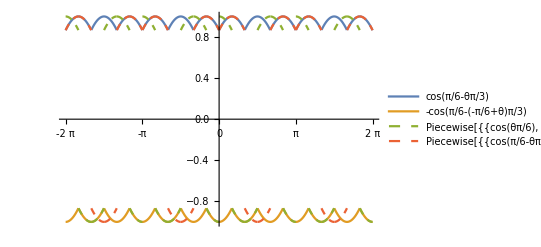

```mathematica
Row[{"fR"[θ],"=", ApplyToPiecewise[mForm,fSO[fSe[θ1],θ]],"⊗",ApplyToPiecewise[mForm,fRO[fRm[θ1,"fRe"],θ]]}]
Plot[Evaluate[{Cos[Mod[θ,Pi/3]-Pi/6],- Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],ApplyToPiecewise[#[[2]]&,fSO[fSe[Mod[θ,Pi/6]],θ]],ApplyToPiecewise[#[[3]]&,fSO[fSe[Mod[θ,Pi/6]],θ]]}],{θ,-2Pi,2Pi},Ticks->{PiTicks[-2Pi,2Pi],All},PlotLegends->"Expressions",PlotStyle->{Thick,Thick,Dashed,Dashed}]
```

Separate the sign from the piecewise function

```mathematica
fSs=Function[{θ},Piecewise[{{{1,1,1}, 0≤Mod[θ,π]<π/6}, {{1,-1,1}, π/6≤Mod[θ,π]<π/3}, {{1,-1,-1}, π/3≤Mod[θ,π]<π/2}, {{1,1,-1}, π/2≤Mod[θ,π]<(2 π)/3}, {{1,1,1}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1,-1,1}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]];

fSseDev=FullSimplify[Piecewise[{{{1,Cos[Mod[θ,π/6]],Cos[π/6-Mod[θ,π/6]]}, 0≤Mod[θ,π]<π/6}, {{1,Cos[π/6-Mod[θ,π/6]],Cos[Mod[θ,π/6]]}, π/6≤Mod[θ,π]<π/3}, {{1,Cos[Mod[θ,π/6]],Cos[π/6-Mod[θ,π/6]]}, π/3≤Mod[θ,π]<π/2}, {{1,Cos[π/6-Mod[θ,π/6]],Cos[Mod[θ,π/6]]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1,Cos[Mod[θ,π/6]],Cos[π/6-Mod[θ,π/6]]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1,Cos[π/6-Mod[θ,π/6]],Cos[Mod[θ,π/6]]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]];
```

```mathematica
Row[{"fS"[θ],"=", ApplyToPiecewise[mForm,fSs[θ]],"⊗",ApplyToPiecewise[mForm,fSseDev]}]
```

fS[θ]=Piecewise[{{1
1
1, 0≤Mod[θ,π]<π/6}, {1
-1
1, π/6≤Mod[θ,π]<π/3}, {1
-1
-1, π/3≤Mod[θ,π]<π/2}, {1
1
-1, π/2≤Mod[θ,π]<(2 π)/3}, {1
1
1, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-1
1, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]⊗Piecewise[{{1
cos(π/6 - TemplateBox[List[
cos(TemplateBox[List[, π/6≤Mod[θ,π]<π/3||π/2≤Mod[θ,π]<(2 π)/3||(5 π)/6≤Mod[θ,π]<π}, {1
cos(TemplateBox[List[
cos(π/6 - TemplateBox[List[, 0≤Mod[θ,π]<π/6||π/3≤Mod[θ,π]<π/2||(2 π)/3≤Mod[θ,π]<(5 π)/6}, {0, True}}]

The Functions can be combined

```mathematica
Clear[fSse];fSse=Function[{θ},{1,Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],Cos[Mod[θ,Pi/3]-Pi/6]}];
Row[{"fSe"[θ],"=",MatrixForm[fSse[θ]], "=",ApplyToPiecewise[MatrixForm,fSseDev]}]
```

fSe[θ]=(1
Cos[π/6-Mod[-π/6+θ,π/3]]
Cos[π/6-Mod[θ,π/3]])=Piecewise[{{(1
Cos[π/6-Mod[θ,π/6]]
Cos[Mod[θ,π/6]]), π/6≤Mod[θ,π]<π/3||π/2≤Mod[θ,π]<(2 π)/3||(5 π)/6≤Mod[θ,π]<π}, {(1
Cos[Mod[θ,π/6]]
Cos[π/6-Mod[θ,π/6]]), 0≤Mod[θ,π]<π/6||π/3≤Mod[θ,π]<π/2||(2 π)/3≤Mod[θ,π]<(5 π)/6}, {0, True}}]

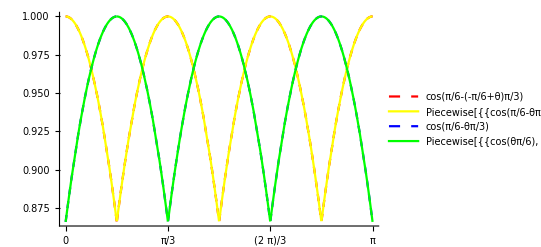

```mathematica
Plot[Evaluate[{fSse[θ][[2]],ApplyToPiecewise[#[[2]]&,fSseDev],fSse[θ][[3]],ApplyToPiecewise[#[[3]]&,fSseDev]}],{θ,0,Pi},Ticks->{PiTicks[0,Pi],All},PlotLegends->"Expressions",PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]}]
```

```mathematica
Row[{ApplyToPiecewise[mForm,fSO[fSe[θ1],θ]],"=", ApplyToPiecewise[mForm,fSse[θ]],"⊗",ApplyToPiecewise[mForm,fSs[θ]]}]
```

Piecewise[{{1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), π/6≤Mod[θ,π]<π/3}, {1
-cos(TraditionalForm`θ_1)
-cos(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - TraditionalForm`θ_1)
-cos(TraditionalForm`θ_1), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]=1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[⊗Piecewise[{{1
1
1, 0≤Mod[θ,π]<π/6}, {1
-1
1, π/6≤Mod[θ,π]<π/3}, {1
-1
-1, π/3≤Mod[θ,π]<π/2}, {1
1
-1, π/2≤Mod[θ,π]<(2 π)/3}, {1
1
1, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-1
1, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

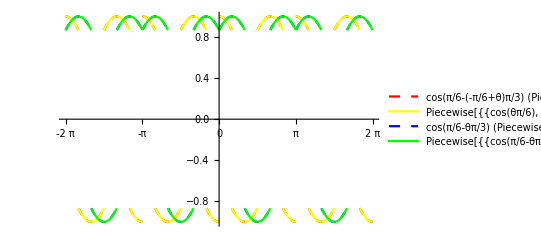

```mathematica
Plot[Evaluate[{fSse[θ][[2]] ApplyToPiecewise[#[[2]]&,fSs[θ]],ApplyToPiecewise[#[[2]]&,fSO[fSe[Mod[θ,Pi/6]],θ]],fSse[θ][[3]] ApplyToPiecewise[#[[3]]&,fSs[θ]],ApplyToPiecewise[#[[3]]&,fSO[fSe[Mod[θ,Pi/6]],θ]]}],{θ,-2Pi,2Pi},Ticks->{PiTicks[-2Pi,2Pi],All},PlotLegends->"Expressions",PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]}]
```

One further simplification if needed.

```mathematica
fSoo=Function[{θ},Piecewise[{{{1,1,1}, 0≤Mod[θ,2π/3]<π/6}, {{1,-1,1}, π/6≤Mod[θ,2π/3]<π/3}, {{1,-1,-1}, π/3≤Mod[θ,2π/3]<π/2}, {{1,1,-1}, π/2≤Mod[θ,2π/3]<(2 π)/3}, {0, True}}]];
fSo=Function[{θ},Piecewise[{{{1,1,1}, 0≤Mod[θ,2Pi]<π}, {{1,-1,-1}, π≤Mod[θ,2Pi]<2 π}, {0, True}}]];
```

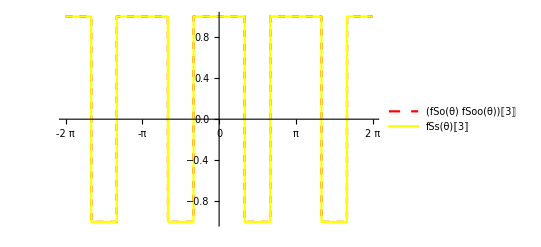

```mathematica
Plot[{(fSo[θ]fSoo[θ])[[3]],fSs[θ][[3]]},{θ,-2Pi,2Pi},PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]},PlotLegends->"Expressions",Ticks->{PiTicks[-2Pi,2Pi],All}]
```

```mathematica
Row[{ApplyToPiecewise[mForm,fSO[fSe[θ1],θ]],"=", ApplyToPiecewise[mForm,fSse[θ]],"⊗",ApplyToPiecewise[mForm,fSo[θ]],"⊗",ApplyToPiecewise[mForm,fSoo[θ]]}]
```

Piecewise[{{1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), π/6≤Mod[θ,π]<π/3}, {1
-cos(TraditionalForm`θ_1)
-cos(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - TraditionalForm`θ_1)
-cos(TraditionalForm`θ_1), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]=1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[⊗Piecewise[{{1
1
1, 0≤Mod[θ,2 π]<π}, {1
-1
-1, π≤Mod[θ,2 π]<2 π}, {0, True}}]⊗Piecewise[{{1
1
1, 0≤Mod[θ,(2 π)/3]<π/6}, {1
-1
1, π/6≤Mod[θ,(2 π)/3]<π/3}, {1
-1
-1, π/3≤Mod[θ,(2 π)/3]<π/2}, {1
1
-1, π/2≤Mod[θ,(2 π)/3]<(2 π)/3}, {0, True}}]

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,1,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,1,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,2,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,2,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,3,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,3,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,4,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,4,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,5,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,5,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,6,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fSe[θ]",FontWeight->Bold],"⊗"}],Row[{Style["fSs[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The Factored Rotation in each π/6 Region
-Graphics- | Scale : fSe[θ]⊗ | fSs[θ] | Factored Rotation : fR[θ]
A | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
1
1 | (1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1)
B | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
-1
1 | (1 | 1 | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1
-fRe(θ_1)-1 | fRe(θ_1) | 1)
C | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
-1
-1 | (1 | 1 | 1
1 | -fRe(θ_1)-1 | fRe(θ_1)
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1))
D | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
1
-1 | (1 | 1 | 1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1)
E | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
1
1 | (1 | 1 | 1
-fRe(θ_1)-1 | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1)
F | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
-1
1 | (1 | 1 | 1
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)
1 | -fRe(θ_1)-1 | fRe(θ_1))

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,1,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,1,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,2,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,2,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,3,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,3,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,4,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,4,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,5,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,5,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,6,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fSe[θ]",FontWeight->Bold],"⊗",Style["fSs[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ] = fRO[fRm[θ1,fRe],θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The Factored Rotation in each π/6 Region
-Graphics- | Scale : fSe[θ]⊗fSs[θ] | Factored Rotation : fR[θ] = fRO[fRm[θ1,fRe],θ]
A | fSe[θ]⊗1
1
1 | (1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1)
B | fSe[θ]⊗1
-1
1 | (1 | 1 | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1
-fRe(θ_1)-1 | fRe(θ_1) | 1)
C | fSe[θ]⊗1
-1
-1 | (1 | 1 | 1
1 | -fRe(θ_1)-1 | fRe(θ_1)
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1))
D | fSe[θ]⊗1
1
-1 | (1 | 1 | 1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1)
E | fSe[θ]⊗1
1
1 | (1 | 1 | 1
-fRe(θ_1)-1 | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1)
F | fSe[θ]⊗1
-1
1 | (1 | 1 | 1
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)
1 | -fRe(θ_1)-1 | fRe(θ_1))

```mathematica
TeXForm[TableForm[{
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,1,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,1,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,2,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,2,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,3,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,3,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,4,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,4,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,5,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,5,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,6,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fSe[θ]",FontWeight->Bold],"⊗",Style["fSs[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ] = fRO[fRm[θ1,fRe],θ]",FontWeight->Bold]}]}},TableAlignments->Center]]
```

\begin{array}{ccc}
  &  &  \\
 \text{A} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}(\delta \theta ) & 1 & \text{fRe}(-\delta \theta ) \\
 \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 \\
\end{array}
\right) \\
 \text{B} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) \\
 \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) & 1 \\
\end{array}
\right) \\
 \text{C} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 1 & \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) \\
 \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) \\
\end{array}
\right) \\
 \text{D} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 \\
 \text{fRe}(\delta \theta ) & 1 & \text{fRe}(-\delta \theta ) \\
\end{array}
\right) \\
 \text{E} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) & 1 \\
 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) \\
\end{array}
\right) \\
 \text{F} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) \\
 1 & \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) \\
\end{array}
\right) \\
\end{array}

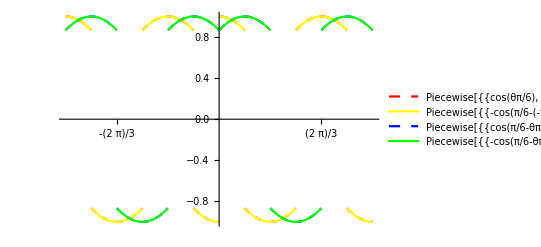

```mathematica
Clear[f,g]
Block[{f,g},
f=Function[{θ},Evaluate[fSO[fSe[Mod[θ,π/6]],θ]]];
fa=Function[{θ},Evaluate[ApplyToPiecewise[#[[2]]&,f[θ]]]];
fb=Function[{θ},Evaluate[ApplyToPiecewise[#[[3]]&,f[θ]]]];

g=Function[{θ},Evaluate[Assuming[Element[θ,Reals],ApplyToPiecewise[(fSse[θ]#)&,PiecewiseExpand[fSo[θ] fSoo[θ]]]]]];
ga=Function[{θ},Evaluate[ApplyToPiecewise[#[[2]]&,g[θ]]]];
gb=Function[{θ},Evaluate[ApplyToPiecewise[#[[3]]&,g[θ]]]];

Plot[Evaluate[{fa[θ],ga[θ],fb[θ],gb[θ]}],{θ,-Pi,Pi},PlotRange->{{-Pi,Pi},{-1,1}},PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]},Ticks->{PiTicks[-2Pi,2Pi],All},PlotLegends->"Expressions"]
]
```

#### The complete transform

```mathematica
scale["nLCaCb","fRs"]=scale["nLCaCb","LCaCb"][θ] scale["LCaCb","rR"][θ]fSse[θ]
```

{1/3,1/2,1/2}

```mathematica
scale["nLCaCb","fRs"]={1/3,1/2,1/2}
```

```mathematica
scale["nLCaCb","fRs"]=scale["nLCaCb","LCaCb"][θ] scale["LCaCb","rR"][θ]fSse[θ];
Row[{nR["θ"]," = ","nS"[θ]," ⊗ ","rS"," ⊗ ","fSse"[θ]," ⊗ ","fSs"[θ]," ⊗ ","fRO"["fRm"[θ1,"fRe"],θ]}]
Row[{"S"[θ]," = ","nS"[θ]," ⊗ ","rS"," ⊗ ","fSse"[θ]," = ",ApplyToPiecewise[mForm,scale["nLCaCb","LCaCb"][θ]],"⊗",mForm[scale["LCaCb","rR"][θ]],"⊗",ApplyToPiecewise[mForm,fSse[θ]]," = ",mForm[scale["nLCaCb","fRs"]]}]
Row[{nR["θ"]," = ","S"[θ]," ⊗ ","fSs"[θ]," ⊗ ","fRO"["fRm"[θ1,"fRe"],θ]}]
```

nR[θ] = nS[θ] ⊗ rS ⊗ fSse[θ] ⊗ fSs[θ] ⊗ fRO[fRm[θ1,fRe],θ]

S[θ] = nS[θ] ⊗ rS ⊗ fSse[θ] = ( TagBox[GridBox[{{1/√3}, {1/2 √3/2 sec(π/6 - TemplateBox[List[RowBox[List[⊗( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] )⊗1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ = ( TagBox[GridBox[{{1/3}, {1/2}, {1/2}}, ColumnAlignments -> Center, RowSpacings -> 1, ColumnAlignments -> Left], Column] )

nR[θ] = S[θ] ⊗ fSs[θ] ⊗ fRO[fRm[θ1,fRe],θ]

```mathematica
nR["θ"]" = ""S"[θ]" ⊗ ""fSs"[θ]" ⊗ ""fRO"["fRm"[θ1,"fRe"],θ]
```

nR[θ] = S[θ] ⊗ fSs[θ] ⊗ fRO[fRm[θ1,fRe],θ]

```mathematica
Row[{nR["θ"]," = ","S"[θ]," ⊗ ",PiecewiseExpand[ApplyToPiecewise[mForm,fSs[θ]] ⊗ ApplyToPiecewise[mForm,fRO[fRm[θ1,"fRe"],θ]]]}]
```

nR[θ] = S[θ] ⊗ Piecewise[{{0⊗0, Mod[θ,π]≥π||Mod[θ,π]<0}, {1
-1
-1⊗1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1
-1
1⊗1 | 1 | 1
1 | fRe | -
- | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1
-1
1⊗1 | 1 | 1
- | 1 | fRe
1 | - | fRe, (5 π)/6≤Mod[θ,π]<π}, {1
1
-1⊗1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π/2≤Mod[θ,π]<(2 π)/3}, {1
1
1⊗1 | 1 | 1
- | fRe | 1
1 | fRe | -, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
1
1⊗1 | 1 | 1
fRe | 1 | -
fRe | - | 1, True}}]

```mathematica
Clear[gR,f];
gR=Function[{θ1,θ,f},Evaluate[Piecewise[Table[{Row[{MatrixForm[fSs[θ][[1,i,1]]]," ⊗ ",MatrixForm[fRO[fRm[θ1,f],θ][[1,i,1]]]}],fSs[θ][[1,i,2]]},{i,1,6}]]]];
Row[{nR["θ"]," = ",mForm[scale["nLCaCb","fRs"]]," ⊗ ",gR[θ1,θ,"fRe"]}]
```

nR[θ] = ( TagBox[GridBox[{{1/3}, {1/2}, {1/2}}, ColumnAlignments -> Center, RowSpacings -> 1, ColumnAlignments -> Left], Column] ) ⊗ Piecewise[{{(1
1
1) ⊗ (1 | 1 | 1
fRe[θ1] | 1 | -1-fRe[θ1]
fRe[π/6-θ1] | -1-fRe[π/6-θ1] | 1), 0≤Mod[θ,π]<π/6}, {(1
-1
1) ⊗ (1 | 1 | 1
1 | fRe[π/6-θ1] | -1-fRe[π/6-θ1]
-1-fRe[θ1] | fRe[θ1] | 1), π/6≤Mod[θ,π]<π/3}, {(1
-1
-1) ⊗ (1 | 1 | 1
1 | -1-fRe[θ1] | fRe[θ1]
-1-fRe[π/6-θ1] | 1 | fRe[π/6-θ1]), π/3≤Mod[θ,π]<π/2}, {(1
1
-1) ⊗ (1 | 1 | 1
fRe[π/6-θ1] | -1-fRe[π/6-θ1] | 1
fRe[θ1] | 1 | -1-fRe[θ1]), π/2≤Mod[θ,π]<(2 π)/3}, {(1
1
1) ⊗ (1 | 1 | 1
-1-fRe[θ1] | fRe[θ1] | 1
1 | fRe[π/6-θ1] | -1-fRe[π/6-θ1]), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {(1
-1
1) ⊗ (1 | 1 | 1
-1-fRe[π/6-θ1] | 1 | fRe[π/6-θ1]
1 | -1-fRe[θ1] | fRe[θ1]), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
Row[{nR["θ"]," = ","S"[θ]," ⊗ ","fSs"[θ]," ⊗ ","fRO"["fRm"[θ1,"fRe"],θ]}]
```

nR[θ] = S[θ] ⊗ fSs[θ] ⊗ fRO[fRm[θ1,fRe],θ]

```mathematica
fSse[θ]
```

{1,Cos[π/6-Mod[-π/6+θ,π/3]],Cos[π/6-Mod[θ,π/3]]}

So we have

```mathematica
fRe=Function[{θ},-1/2 (1+√3 Tan[θ])];
```

```mathematica
fRa=Function[{θ1,f},{{1,1,1},{f[θ1],1,-1-f[θ1]},{f[π/6-θ1],-1-f[π/6-θ1],1}}];
```

```mathematica
fRO=Function[{m,θ},Piecewise[{{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,1⟧,m⟦2,2⟧,m⟦2,3⟧},{m⟦3,1⟧,m⟦3,2⟧,m⟦3,3⟧}}, 0≤Mod[θ,π]<π/6}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,3⟧,m⟦3,1⟧,m⟦3,2⟧},{m⟦2,3⟧,m⟦2,1⟧,m⟦2,2⟧}}, π/6≤Mod[θ,π]<π/3}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,2⟧,m⟦2,3⟧,m⟦2,1⟧},{m⟦3,2⟧,m⟦3,3⟧,m⟦3,1⟧}}, π/3≤Mod[θ,π]<π/2}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,1⟧,m⟦3,2⟧,m⟦3,3⟧},{m⟦2,1⟧,m⟦2,2⟧,m⟦2,3⟧}}, π/2≤Mod[θ,π]<(2 π)/3}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,3⟧,m⟦2,1⟧,m⟦2,2⟧},{m⟦3,3⟧,m⟦3,1⟧,m⟦3,2⟧}}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,2⟧,m⟦3,3⟧,m⟦3,1⟧},{m⟦2,2⟧,m⟦2,3⟧,m⟦2,1⟧}}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]];
```

```mathematica
δqAS=Function[{θ},Piecewise[{{{1,1,0}, 0≤Mod[θ,π]<π/3}, {{1,0,1}, π/3≤Mod[θ,π]<(2 π)/3}, {{0,1,1}, (2 π)/3≤Mod[θ,π]<π}, {0, True}}]];
δqSO=Function[{list,θ},Piecewise[{{{list[[1]],list[[2]],list[[3]]}, 0≤Mod[θ,π/3]<π/6}, {{list[[1]],list[[3]],list[[2]]}, π/6≤Mod[θ,π/3]<π/3}, {0, True}}]];
```

```mathematica
FullSimplify[δqAS[θ]
```

Piecewise[{{{1,1,0}, 0≤Mod[θ,π]<π/3}, {{1,0,1}, π/3≤Mod[θ,π]<(2 π)/3}, {{0,1,1}, (2 π)/3≤Mod[θ,π]<π}, {0, True}}]

```mathematica
δs={{0,0,0},{1,0,-1},{1,-1,0}}
TraditionalForm[Row[{"δqS"[θ]," = fRO"[δs,θ]," = ",fRO[δs,θ]}]]
TraditionalForm[Row[{Abs["δqS"[θ]]," = fRO"[Abs[δs],θ]," = ",Simplify[Abs[fRO[δs,θ]]]}]]
TraditionalForm[Row[{Abs["δqS"[θ]]," = ",{"OverVector[0]","δqAS"[θ+π/2],"δqAS"[θ]}," = ",Simplify[{{0,0,0},δqAS[θ+π/2],δqAS[θ]}]}]]
```

{{0,0,0},{1,0,-1},{1,-1,0}}

δqS(θ) = fRO((0 | 0 | 0
1 | 0 | -1
1 | -1 | 0),θ) = Piecewise[{{(0 | 0 | 0
1 | 0 | -1
1 | -1 | 0), 0≤θπ<π/6}, {(0 | 0 | 0
0 | 1 | -1
-1 | 1 | 0), π/6≤θπ<π/3}, {(0 | 0 | 0
0 | -1 | 1
-1 | 0 | 1), π/3≤θπ<π/2}, {(0 | 0 | 0
1 | -1 | 0
1 | 0 | -1), π/2≤θπ<(2 π)/3}, {(0 | 0 | 0
-1 | 1 | 0
0 | 1 | -1), (2 π)/3≤θπ<(5 π)/6}, {(0 | 0 | 0
-1 | 0 | 1
0 | -1 | 1), (5 π)/6≤θπ<π}}]

Abs[δqS(θ)] = fRO((0 | 0 | 0
1 | 0 | 1
1 | 1 | 0),θ) = Piecewise[{{(0 | 0 | 0
0 | 1 | 1
1 | 0 | 1), π/3≤θπ<π/2}, {(0 | 0 | 0
0 | 1 | 1
1 | 1 | 0), π/6≤θπ<π/3}, {(0 | 0 | 0
1 | 0 | 1
0 | 1 | 1), (5 π)/6≤θπ<π}, {(0 | 0 | 0
1 | 0 | 1
1 | 1 | 0), 0≤θπ<π/6}, {(0 | 0 | 0
1 | 1 | 0
0 | 1 | 1), (2 π)/3≤θπ<(5 π)/6}, {(0 | 0 | 0
1 | 1 | 0
1 | 0 | 1), π/2≤θπ<(2 π)/3}}]

Abs[δqS(θ)] = {OverVector[0],δqAS(θ+π/2),δqAS(θ)} = {{0,0,0},Piecewise[{{{1,1,0}, 0≤(θ+π/2)π<π/3}, {{1,0,1}, π/3≤(θ+π/2)π<(2 π)/3}, {{0,1,1}, (2 π)/3≤(θ+π/2)π<π}}],Piecewise[{{{1,1,0}, 0≤θπ<π/3}, {{1,0,1}, π/3≤θπ<(2 π)/3}, {{0,1,1}, (2 π)/3≤θπ<π}}]}

```mathematica
Table[{θ,absδqS[θ]},{θ,π/12,π,π/6}]
Table[{θ,MatrixForm[{{0,0,0}, absδqS[θ+π/2],absδqS[θ]}]},{θ,π/12,π,π/6}]
```

{{π/12,{1,1,0}},{π/4,{1,1,0}},{(5 π)/12,{1,0,1}},{(7 π)/12,{1,0,1}},{(3 π)/4,{0,1,1}},{(11 π)/12,{0,1,1}}}

{{π/12,(0 | 0 | 0
1 | 0 | 1
1 | 1 | 0)},{π/4,(0 | 0 | 0
0 | 1 | 1
1 | 1 | 0)},{(5 π)/12,(0 | 0 | 0
0 | 1 | 1
1 | 0 | 1)},{(7 π)/12,(0 | 0 | 0
1 | 1 | 0
1 | 0 | 1)},{(3 π)/4,(0 | 0 | 0
1 | 1 | 0
0 | 1 | 1)},{(11 π)/12,(0 | 0 | 0
1 | 0 | 1
0 | 1 | 1)}}

```mathematica
fSe= Function[{θ1},{1,Cos[θ1],Cos[π/6-θ1]}];
fSO = Function[{m, θ}, Piecewise[{{{1, m[[2]], m[[3]]}, Inequality[0, LessEqual, 
       Mod[θ, Pi], Less, Pi/6]}, {{1, -m[[3]], m[[2]]}, Inequality[Pi/6, LessEqual, 
       Mod[θ, Pi], Less, Pi/3]}, {{1, -m[[2]], -m[[3]]}, Inequality[Pi/3, LessEqual, 
       Mod[θ, Pi], Less, Pi/2]}, {{1, m[[3]], -m[[2]]}, Inequality[Pi/2, LessEqual, 
       Mod[θ, Pi], Less, (2*Pi)/3]}, {{1, m[[2]], m[[3]]}, 
      Inequality[(2*Pi)/3, LessEqual, Mod[θ, Pi], Less, (5*Pi)/6]}, 
     {{1, -m[[3]], m[[2]]}, Inequality[(5*Pi)/6, LessEqual, Mod[θ, Pi], Less, Pi]}}, 0]];
fSO[fSe[θ1],θ]
```

```mathematica
Piecewise[{{{1,Cos[θ1],Cos[π/6-θ1]}, 0≤Mod[θ,π]<π/6}, {{1,-Cos[π/6-θ1],Cos[θ1]}, π/6≤Mod[θ,π]<π/3}, {{1,-Cos[θ1],-Cos[π/6-θ1]}, π/3≤Mod[θ,π]<π/2}, {{1,Cos[π/6-θ1],-Cos[θ1]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1,Cos[θ1],Cos[π/6-θ1]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1,-Cos[π/6-θ1],Cos[θ1]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]
```

```mathematica
Clear[ϕ]
m={{1,1,1},{a,1,α},{b,β,1}};
δm={{0,0,0},{a,0,-a},{b,-b,0}};
TraditionalForm@Column[{
Row[{"fR(θ) = fRO( fRa( θ1, fRe))"}],
Row[{θ1," = ",Mod[θ,π/6]}],
Row[{"fRe(ϕ) = ",fRe[ϕ]}],
Row[{"fRa"[ϕ, f]," = ",fRa[ϕ,f]}],
Row[{"fRO"[mForm[m],θ]," = ",fRO[m,θ]}]
}]
```

fR(θ) = fRO( fRa( θ1, fRe))
θ_1 = θπ/6
fRe(ϕ) = 1/2 (-√3 tan(ϕ)-1)
fRa(ϕ,f) = fRa(ϕ,f)
fRO(1 | 1 | 1
a | 1 | α
b | β | 1,θ) = Piecewise[{{(1 | 1 | 1
a | 1 | α
b | β | 1), 0≤θπ<π/6}, {(1 | 1 | 1
1 | b | β
α | a | 1), π/6≤θπ<π/3}, {(1 | 1 | 1
1 | α | a
β | 1 | b), π/3≤θπ<π/2}, {(1 | 1 | 1
b | β | 1
a | 1 | α), π/2≤θπ<(2 π)/3}, {(1 | 1 | 1
α | a | 1
1 | b | β), (2 π)/3≤θπ<(5 π)/6}, {(1 | 1 | 1
β | 1 | b
1 | α | a), (5 π)/6≤θπ<π}}]

```mathematica
Table[{θ,MatrixForm[{{0,0,0},absδqS[θ+π/2],absδqS[θ]}]},{θ,π/12,π,π/6}]
```

{{π/12,(0 | 0 | 0
1 | 0 | 1
1 | 1 | 0)},{π/4,(0 | 0 | 0
0 | 1 | 1
1 | 1 | 0)},{(5 π)/12,(0 | 0 | 0
0 | 1 | 1
1 | 0 | 1)},{(7 π)/12,(0 | 0 | 0
1 | 1 | 0
1 | 0 | 1)},{(3 π)/4,(0 | 0 | 0
1 | 1 | 0
0 | 1 | 1)},{(11 π)/12,(0 | 0 | 0
1 | 0 | 1
0 | 1 | 1)}}

```mathematica
TraditionalForm[Row[{"fRO"[δm,θ]," = ",fRO[δm,θ]}]]
TeXForm[fRO[δm,θ]]
```

fRO((0 | 0 | 0
a | 0 | -a
b | -b | 0),θ) = Piecewise[{{(0 | 0 | 0
a | 0 | -a
b | -b | 0), 0≤θπ<π/6}, {(0 | 0 | 0
0 | b | -b
-a | a | 0), π/6≤θπ<π/3}, {(0 | 0 | 0
0 | -a | a
-b | 0 | b), π/3≤θπ<π/2}, {(0 | 0 | 0
b | -b | 0
a | 0 | -a), π/2≤θπ<(2 π)/3}, {(0 | 0 | 0
-a | a | 0
0 | b | -b), (2 π)/3≤θπ<(5 π)/6}, {(0 | 0 | 0
-b | 0 | b
0 | -a | a), (5 π)/6≤θπ<π}}]

```mathematica
Manipulate[Column[{StringJoin["rR[",ToString[θ,TraditionalForm],"] = ",mForm[colorMat[rR[θ]]]],StringJoin[mForm[scale["rR","fR"][θ]],"⊗",mForm[fR[θ]]," == ",mForm[rR[θ]],If[rR[θ]== scale["rR","fR"][θ]  fR[θ],"✓","×"]]}],{θ,0,2 Pi}]
```

StringJoin::string: String expected at position 2 in "rR[\!\(TraditionalForm\`0\)] = " <> mForm[colorMat[rR[0]]].

StringJoin::string: String expected at position 1 in mForm[scale["rR", "fR"][0]] <> "\[CircleTimes]" <> mForm[fR[0]] <> " == " <> mForm[rR[0]] <> If[rR[0] == fR[0]\ scale["rR", "fR"][0], "\[Checkmark]", "\[Times]"].

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### The quantized representation

fR has elements which are in the range -1 ... 1.
These can be scaled to an integer range for discrete representation as qR. 
The scale we choose depends on the bit depth of the target type. To sum three numbers of one type requires one bit per sum. If the src type is n bits and we wish to represent the matrix in the same type, allowing that the working type be 2n bits and not more, then the matrix must be represented in n-2 bits.

```mathematica
Row[{qR["θ"]," = Round[",mForm[scale["qR","fR"][θ,n]],"⊗",fR["θ"],"]   where   ",TraditionalForm[scale["qR","fR"]["θ",n]]," = ",mForm[scale["qR","fR"][θ,n]]}]
```

qR[θ] = Round[1
2^n - 2
2^n - 2⊗fR[θ]]   where   qS^-1(θ,n) = 1
2^n - 2
2^n - 2

```mathematica
qRmFun=Function[{θ1,f,n},Evaluate[Assuming[Element[n,Integers]&&n>3,Simplify[Round[Expand[scale["qR","fR"][θ,n] fRm[θ1,f]]]/.{Round[Plus[a_,b__]]-> Plus[Round[a],Round[b]]}]]]];
qRFun=Function[{θ6,θ1,f,n},Evaluate[fROFun[qRmFun[θ1,f,n],θ6]]];
Clear[qR]
qR[θ6:Except[_String],θ1_,fReqq_,n_]:=qRFun[θ6,θ1,fReqq,n];
qR[θ:Except[_String],fReqq_,n_]:=qRFun[Mod[θ,π],Mod[θ,π/6],fReqq,n];
qR[θ:Except[_String],n_]:=qRFun[Mod[θ,π],Mod[θ,π/6],fRe,n];
qR[θ:Except[_String]]:=qRFun[Mod[θ,π],Mod[θ,π/6],fRe,8];
```

```mathematica
Style[TraditionalForm[Row[{"qRm = ",MatrixForm[qRmFun[θ1,"fRe",n]]}]],Larger]
Style[TraditionalForm[Row[{qR["θ"]," = ",fRO[qRm["θ_1","fRe",n],"θ_6"],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]],Larger]
Style[TraditionalForm[Row[{ShowFun[qR[θ6,θ1,"fRe",n]],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]],Larger]
```

qRm = (1 | 1 | 1
Round[2^(n-2) fRe(θ_1)] | 2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2)
Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2))

qR(θ) = fRO(qRm(θ_1,fRe,n),θ_6)  where  fRe = 1/2 (-√3 tan(θ)-1)
θ_1 = θπ/6
θ_6 = θπ

qR(θ6,θ1,fRe,n) = Piecewise[{{(1 | 1 | 1
Round[2^(n-2) fRe(θ_1)] | 2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2)
Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2)), 0≤θ_6<π/6}, {(1 | 1 | 1
2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2)
-Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)] | 2^(n-2)), π/6≤θ_6<π/3}, {(1 | 1 | 1
2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)]
-Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)]), π/3≤θ_6<π/2}, {(1 | 1 | 1
Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2)
Round[2^(n-2) fRe(θ_1)] | 2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2)), π/2≤θ_6<(2 π)/3}, {(1 | 1 | 1
-Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)] | 2^(n-2)
2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2)), (2 π)/3≤θ_6<(5 π)/6}, {(1 | 1 | 1
-Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)]
2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)]), (5 π)/6≤θ_6<π}}]  where  fRe = 1/2 (-√3 tan(θ)-1)
θ_1 = θπ/6
θ_6 = θπ

```mathematica
δqRmFun=Function[{θ1,f,n},Evaluate[Assuming[Element[n,Integers]&&n>3,Simplify[Expand[scale["qR","fR"][θ,n] fRm[θ1,f] - qRmFun[θ1,f,n]]] ]]];
δqRm[θ:Except[_String],fReqq_,n_]:=δqRmFun[Mod[θ,π/6],fReqq,n];
δqRm[θ:Except[_String],n_]:=δqRmFun[Mod[θ,π/6],fRe,n];
δqRm[θ:Except[_String]]:=δqRmFun[Mod[θ,π/6],fRe,8];
TraditionalForm[δqRmFun[θ1,"fRe",n]];
δqRFun=Function[{θ6,θ1,f,n},Evaluate[fROFun[δqRmFun[θ1,f,n],θ6]]];
Clear[δqR]
δqR[θ6:Except[_String],θ1_,fReqq_,n_]:=δqRFun[θ6,θ1,fReqq,n];
δqR[θ:Except[_String],fReqq_,n_]:=δqRFun[Mod[θ,π],Mod[θ,π/6],fReqq,n];
δqR[θ:Except[_String],n_]:=δqRFun[Mod[θ,π],Mod[θ,π/6],fRe,n];
δqR[θ:Except[_String]]:=δqRFun[Mod[θ,π],Mod[θ,π/6],fRe,8];
```

```mathematica
Style[TraditionalForm[Row[{"δqR = ",MatrixForm[δqRmFun[θ1,"fRe",n]]}]],Larger]
Style[TraditionalForm[Row[{δqR["θ"]," = ",fRO[δqRm["θ_1","fRe",n],"θ_6"],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]],Larger]
Style[TraditionalForm[Row[{ShowFun[δqR[θ6,θ1,"fRe",n]],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]],Larger]
```

δqR = (0 | 0 | 0
2^(n-2) fRe(θ_1)-Round[2^(n-2) fRe(θ_1)] | 0 | Round[2^(n-2) fRe(θ_1)]-2^(n-2) fRe(θ_1)
2^(n-2) fRe(π/6-θ_1)-Round[2^(n-2) fRe(π/6-θ_1)] | Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) fRe(π/6-θ_1) | 0)

δqR(θ) = fRO(δqRm(θ_1,fRe,n),θ_6)  where  fRe = 1/2 (-√3 tan(θ)-1)
θ_1 = θπ/6
θ_6 = θπ

δqR(θ6,θ1,fRe,n) = Piecewise[{{(0 | 0 | 0
2^(n-2) fRe(θ_1)-Round[2^(n-2) fRe(θ_1)] | 0 | Round[2^(n-2) fRe(θ_1)]-2^(n-2) fRe(θ_1)
2^(n-2) fRe(π/6-θ_1)-Round[2^(n-2) fRe(π/6-θ_1)] | Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) fRe(π/6-θ_1) | 0), 0≤θ_6<π/6}, {(0 | 0 | 0
0 | 2^(n-2) fRe(π/6-θ_1)-Round[2^(n-2) fRe(π/6-θ_1)] | Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) fRe(π/6-θ_1)
Round[2^(n-2) fRe(θ_1)]-2^(n-2) fRe(θ_1) | 2^(n-2) fRe(θ_1)-Round[2^(n-2) fRe(θ_1)] | 0), π/6≤θ_6<π/3}, {(0 | 0 | 0
0 | Round[2^(n-2) fRe(θ_1)]-2^(n-2) fRe(θ_1) | 2^(n-2) fRe(θ_1)-Round[2^(n-2) fRe(θ_1)]
Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) fRe(π/6-θ_1) | 0 | 2^(n-2) fRe(π/6-θ_1)-Round[2^(n-2) fRe(π/6-θ_1)]), π/3≤θ_6<π/2}, {(0 | 0 | 0
2^(n-2) fRe(π/6-θ_1)-Round[2^(n-2) fRe(π/6-θ_1)] | Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) fRe(π/6-θ_1) | 0
2^(n-2) fRe(θ_1)-Round[2^(n-2) fRe(θ_1)] | 0 | Round[2^(n-2) fRe(θ_1)]-2^(n-2) fRe(θ_1)), π/2≤θ_6<(2 π)/3}, {(0 | 0 | 0
Round[2^(n-2) fRe(θ_1)]-2^(n-2) fRe(θ_1) | 2^(n-2) fRe(θ_1)-Round[2^(n-2) fRe(θ_1)] | 0
0 | 2^(n-2) fRe(π/6-θ_1)-Round[2^(n-2) fRe(π/6-θ_1)] | Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) fRe(π/6-θ_1)), (2 π)/3≤θ_6<(5 π)/6}, {(0 | 0 | 0
Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) fRe(π/6-θ_1) | 0 | 2^(n-2) fRe(π/6-θ_1)-Round[2^(n-2) fRe(π/6-θ_1)]
0 | Round[2^(n-2) fRe(θ_1)]-2^(n-2) fRe(θ_1) | 2^(n-2) fRe(θ_1)-Round[2^(n-2) fRe(θ_1)]), (5 π)/6≤θ_6<π}}]  where  fRe = 1/2 (-√3 tan(θ)-1)
θ_1 = θπ/6
θ_6 = θπ

```mathematica
δqRmFun=Function[{θ1,f,n},Evaluate[Assuming[Element[n,Integers]&&n>3,Simplify[Expand[scale["qR","fR"][θ,n] fRm[θ1,f] - qRmFun[θ1,f,n]]] ]]];
δqRm[θ:Except[_String],fReqq_,n_]:=δqRmFun[Mod[θ,π/6],fReqq,n];
δqRm[θ:Except[_String],n_]:=δqRmFun[Mod[θ,π/6],fRe,n];
δqRm[θ:Except[_String]]:=δqRmFun[Mod[θ,π/6],fRe,8];
TraditionalForm[δqRmFun[θ1,"fRe",n]];
δqRFun=Function[{θ6,θ1,f,n},Evaluate[fROFun[δqRmFun[θ1,f,n],θ6]]];
Clear[δqR]
δqR[θ6:Except[_String],θ1_,fReqq_,n_]:=δqRFun[θ6,θ1,fReqq,n];
δqR[θ:Except[_String],fReqq_,n_]:=δqRFun[Mod[θ,π],Mod[θ,π/6],fReqq,n];
δqR[θ:Except[_String],n_]:=δqRFun[Mod[θ,π],Mod[θ,π/6],fRe,n];
δqR[θ:Except[_String]]:=δqRFun[Mod[θ,π],Mod[θ,π/6],fRe,8];
```

```mathematica
fRs[θ1,f]
```

Piecewise[{{{{1,1,1},{-1,-f[π/6-Mod[θ1,π/6]],1+f[π/6-Mod[θ1,π/6]]},{-1-f[Mod[θ1,π/6]],f[Mod[θ1,π/6]],1}}, π/6≤Mod[θ1,π]<π/3}, {{{1,1,1},{-1,1+f[Mod[θ1,π/6]],-f[Mod[θ1,π/6]]},{1+f[π/6-Mod[θ1,π/6]],-1,-f[π/6-Mod[θ1,π/6]]}}, π/3≤Mod[θ1,π]<π/2}, {{{1,1,1},{f[π/6-Mod[θ1,π/6]],-1-f[π/6-Mod[θ1,π/6]],1},{-f[Mod[θ1,π/6]],-1,1+f[Mod[θ1,π/6]]}}, π/2≤Mod[θ1,π]<(2 π)/3}, {{{1,1,1},{1+f[π/6-Mod[θ1,π/6]],-1,-f[π/6-Mod[θ1,π/6]]},{1,-1-f[Mod[θ1,π/6]],f[Mod[θ1,π/6]]}}, (5 π)/6≤Mod[θ1,π]<π}, {{{1,1,1},{-1-f[Mod[θ1,π/6]],f[Mod[θ1,π/6]],1},{1,f[π/6-Mod[θ1,π/6]],-1-f[π/6-Mod[θ1,π/6]]}}, (2 π)/3≤Mod[θ1,π]<(5 π)/6}, {{{1,1,1},{f[Mod[θ1,π/6]],1,-1-f[Mod[θ1,π/6]]},{f[π/6-Mod[θ1,π/6]],-1-f[π/6-Mod[θ1,π/6]],1}}, 0≤Mod[θ1,π]<π/6}, {0, True}}]

```mathematica
ApplyToPiecewise[MatrixForm,ApplyToPiecewise[Simplify,PiecewiseExpand[ApplyToPiecewise[Times[scale["qR","fR"][θ,n],#]&, fRs[θ6,θ1,fReqq]]- qRs[θ6,θ1,fReqq,n]]]]
```

Piecewise[{{(0 | 0 | 0
0 | -2^(-2+n) fReqq[π/6-θ1]+Round[2^(-2+n) fReqq[π/6-θ1]] | 2^(-2+n) fReqq[π/6-θ1]-Round[2^(-2+n) fReqq[π/6-θ1]]
-2^(-2+n) fReqq[θ1]+Round[2^(-2+n) fReqq[θ1]] | 2^(-2+n) fReqq[θ1]-Round[2^(-2+n) fReqq[θ1]] | 0), π/6≤θ6<π/3}, {(0 | 0 | 0
0 | 2^(-2+n) fReqq[θ1]-Round[2^(-2+n) fReqq[θ1]] | -2^(-2+n) fReqq[θ1]+Round[2^(-2+n) fReqq[θ1]]
2^(-2+n) fReqq[π/6-θ1]-Round[2^(-2+n) fReqq[π/6-θ1]] | 0 | -2^(-2+n) fReqq[π/6-θ1]+Round[2^(-2+n) fReqq[π/6-θ1]]), π/3≤θ6<π/2}, {(0 | 0 | 0
2^(-2+n) fReqq[π/6-θ1]-Round[2^(-2+n) fReqq[π/6-θ1]] | -2^(-2+n) fReqq[π/6-θ1]+Round[2^(-2+n) fReqq[π/6-θ1]] | 0
-2^(-2+n) fReqq[θ1]+Round[2^(-2+n) fReqq[θ1]] | 0 | 2^(-2+n) fReqq[θ1]-Round[2^(-2+n) fReqq[θ1]]), π/2≤θ6<(2 π)/3}, {(0 | 0 | 0
2^(-2+n) fReqq[π/6-θ1]-Round[2^(-2+n) fReqq[π/6-θ1]] | 0 | -2^(-2+n) fReqq[π/6-θ1]+Round[2^(-2+n) fReqq[π/6-θ1]]
0 | -2^(-2+n) fReqq[θ1]+Round[2^(-2+n) fReqq[θ1]] | 2^(-2+n) fReqq[θ1]-Round[2^(-2+n) fReqq[θ1]]), (5 π)/6≤θ6<π}, {(0 | 0 | 0
2^(-2+n) fReqq[θ1]-Round[2^(-2+n) fReqq[θ1]] | 0 | -2^(-2+n) fReqq[θ1]+Round[2^(-2+n) fReqq[θ1]]
2^(-2+n) fReqq[π/6-θ1]-Round[2^(-2+n) fReqq[π/6-θ1]] | -2^(-2+n) fReqq[π/6-θ1]+Round[2^(-2+n) fReqq[π/6-θ1]] | 0), 0≤θ6<π/6}, {(0 | 0 | 0
-2^(-2+n) fReqq[θ1]+Round[2^(-2+n) fReqq[θ1]] | 2^(-2+n) fReqq[θ1]-Round[2^(-2+n) fReqq[θ1]] | 0
0 | 2^(-2+n) fReqq[π/6-θ1]-Round[2^(-2+n) fReqq[π/6-θ1]] | -2^(-2+n) fReqq[π/6-θ1]+Round[2^(-2+n) fReqq[π/6-θ1]]), (2 π)/3≤θ6<(5 π)/6}, {0, True}}]

```mathematica
PiecewiseExpand[scale["qR","fR"][θ,n] fRs[θ1,f] - qRsFun[θ1,f,n]]
```

{ | 1
 |  |  |  |